```mathematica
(*QuEST VQD Setup*)
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[];
```

```mathematica
Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\vqd CG V3 Parallel.wl"]
```

```mathematica
data=Import["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\SU4Gates9Qubits.csv"];
```

```mathematica
distloc[q1_, q2_] := 
			Norm[RydDev[AtomLocations][q1] - RydDev[AtomLocations][q2], 2] RydDev[UnitLattice];

blockadecheck[q_List] := 
			And @@ ((distloc @@ # <= (RydDev[BlockadeRadius]+$MachineEpsilon))& /@ Subsets[Flatten[q], {2}]);
```

```mathematica
(*VQD Initialisation*)locations=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}];
SWAPlocations=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{2,0,0},{2,1,0},{3,0,0},{3,1,0},{4,0,0}}}];
ParallelConfig={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> locations
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 10
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.003(*0.007*)
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 100
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
SWAPConfig={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> SWAPlocations
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 1.1
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.003(*0.007*)
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 0
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
MoveTime=100
Options[RydbergHub]=ParallelConfig;
RydDev=RydbergHub[];
PlotAtoms[RydbergHub[]]
```

100

-Graphics3D-

```mathematica
(*Algorithm to determine the necessary operations for any two qubits to share connection*)
(*By "Rail" we mean they are colinear along the x-axis of the grid*)
SWAPSchedulePI[GateData_,A_,B_,LocTrackerPI_]:=Module[
{},
LocTracker=LocTrackerPI;
Which[
(*Same Rail*)

EvenQ[Abs[LocTracker[[A+1]]-LocTracker[[B+1]]]],
(*Print["Same Rail"];*)
If[
LocTracker[[A+1]]==LocTracker[[B+1]]+2||LocTracker[[A+1]]==LocTracker[[B+1]]-2,
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
MaxPosi=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MinPosi=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQi=Flatten[Position[LocTracker,MaxPosi]][[1]]-1;
li=(MaxPosi-MinPosi)/2-1;
(*Print["m= ",li];*)
OutputLayer=Flatten[Join[
Table[
MaxPos=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQ=Flatten[Position[LocTracker,MaxPos]][[1]]-1;
MinPos=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
(*Print["MaxPos ",MaxPos," MinPos ",MinPos, " MaxPosQ ",MaxPosQ ];*)
MoveTarg=Flatten[Position[LocTracker,MaxPos-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,MaxPos-2]][[1]]]]+=2;
LocTracker[[MaxPosQ+1]]-=2;
{Subscript[SWAPDCPIRL, MaxPosQi,MoveTarg],Subscript[SWAPLoc, MoveTarg,MaxPosQi]},
{i,1,li}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],

(*Different rail, A is the top rail*)
OddQ[LocTracker[[A+1]]],
(*Print["A odd, Diff Rail"];*)
Which[
(*Aligned*)
LocTracker[[A+1]]==LocTracker[[B+1]]+1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
(*A Right of B*)
LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " ,A, " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},
{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A left of B*)


LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]-1))/2;

OutputLayer=Flatten[Join[
Table[
(*Print["LocTracker Before ", LocTracker];*)
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " , B, " -> ", MoveTarg];
Print["LocTracker After ", LocTracker];*)
{Subscript[SWAPDCPIRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},
{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],


(*Different rail, B is the top rail*)
OddQ[LocTracker[[ B+1]]],
(*Print["Diff Rail, B top"];*)
Which[
(*Aligned*)

LocTracker[[A+1]]==LocTracker[[B+1]]-1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
(*A right of B*)

LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]-1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " , A, " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A Left of B*)

LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " ,B , " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
]
]]
```

```mathematica
(*Algorithm to determine the necessary operations for any two qubits to share connection*)
(*By "Rail" we mean they are colinear along the x-axis of the grid*)
SWAPScheduleARP[GateData_,A_,B_,LocTrackerARP_]:=Module[
{},
LocTracker=LocTrackerARP;
Which[
(*Same Rail*)

EvenQ[Abs[LocTracker[[A+1]]-LocTracker[[B+1]]]],
(*Print["Same Rail"];*)
If[
LocTracker[[A+1]]==LocTracker[[B+1]]+2||LocTracker[[A+1]]==LocTracker[[B+1]]-2,
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
MaxPosi=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MinPosi=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQi=Flatten[Position[LocTracker,MaxPosi]][[1]]-1;
li=(MaxPosi-MinPosi)/2-1;
(*Print["m= ",li];*)
OutputLayer=Flatten[Join[
Table[
MaxPos=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQ=Flatten[Position[LocTracker,MaxPos]][[1]]-1;
MinPos=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
(*Print["MaxPos ",MaxPos," MinPos ",MinPos, " MaxPosQ ",MaxPosQ ];*)
MoveTarg=Flatten[Position[LocTracker,MaxPos-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,MaxPos-2]][[1]]]]+=2;
LocTracker[[MaxPosQ+1]]-=2;
{Subscript[SWAPDCARPRL, MaxPosQi,MoveTarg],Subscript[SWAPLoc, MoveTarg,MaxPosQi]},
{i,1,li}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],

(*Different rail, A is the top rail*)
OddQ[LocTracker[[A+1]]],
(*Print["A odd, Diff Rail"];*)
Which[
(*Aligned*)
LocTracker[[A+1]]==LocTracker[[B+1]]+1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
(*A Right of B*)
LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " ,A, " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},
{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A left of B*)


LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]-1))/2;

OutputLayer=Flatten[Join[
Table[
(*Print["LocTracker Before ", LocTracker];*)
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " , B, " -> ", MoveTarg];
Print["LocTracker After ", LocTracker];*)
{Subscript[SWAPDCARPRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},
{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],


(*Different rail, B is the top rail*)
OddQ[LocTracker[[ B+1]]],
(*Print["Diff Rail, B top"];*)
Which[
(*Aligned*)

LocTracker[[A+1]]==LocTracker[[B+1]]-1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
(*A right of B*)

LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]-1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " , A, " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A Left of B*)

LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " ,B , " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
]
]]
```

```mathematica
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
LocTrack[Nq_]:=Range[0,Nq-1]
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
NRandQbits[NQ_,i_]:=If[i==0,Range[0,NQ-1],RandomSample[Range[0,NQ-1],NQ]]
(*Randomly generated list, each 2 qubits represent a randomly generated pair*)
QList={0,3,2,7,1,5,6,4,8};

(*Constructed list which replaces the qubit labels with their respective current grid position labels*)
QLoclist=Table[LocTrack[Length[QList]][[QList[[i]]+1]],{i,1,Length[QList]}]

(*Sort the qubit pairs in such a way that the pairs which require the least operations to connect are first in the schedule*)
(*RTN: Pair #, Seperation between qubits as indicator of how many operations needed to connect*)
GateOrdering=SortBy[Table[{i-Quotient[i,2],Abs[QLoclist[[i]]-QLoclist[[i+1]]]},{i,1,Length[QLoclist]-1,2}],Last][[All,1]]
RQSOrd=Flatten[Table[QList[[{2*GateOrdering[[i]]-1,2*GateOrdering[[i]]}]],{i,1,Length[GateOrdering]}]]

CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];
```

{0,3,2,7,1,5,6,4,8}

{4,1,3,2}

{6,4,0,3,1,5,2,7}

```mathematica
SU4GateARPMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]
```

```mathematica
NQ=5
RQs={0,1,2,3,4}
ARPCZdur=1
(*Parallelised SU4 Gate layer generators*)
SU4GateARPParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

SU4GatePIParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZPIPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, ARP CZ*)
SU4GateDCARP[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCARP], a[[1]],a[[2]]],Subscript[CZARP, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, GA CZ*)

SU4GateDCPI[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCPI], a[[1]],a[[2]]],Subscript[CZPI, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
```

5

{0,1,2,3,4}

1

```mathematica
QVLayerARPMove[DataSet_,NQ_,RQs_,i_]:=Join[Table[SU4GateARPMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];

QVLayerPIMove[DataSet_,NQ_,RQs_,i_]:=
Join[Table[SU4GatePIMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];


QVLayerARPParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GateARPParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SpareARP, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]

QVLayerPIParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GatePIParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SparePI, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1];

QVLayerARPPropSWAP[DataSet_,NQ_,RQs_,i_,LocTracker_]:=
Module[{},LocTrackerARP=LocTracker ;Table[
QLoclist=Table[LocTrackerARP[[RQs[[j]]+1]],{j,1,NQ}];

GateOrdering=SortBy[Table[If[EvenQ[QLoclist[[j]]-QLoclist[[j+1]]]&& Abs[QLoclist[[j]]-QLoclist[[j+1]]]==2,{j-Quotient[j,2],0},{j-Quotient[j,2],Abs[QLoclist[[j]]-QLoclist[[j+1]]]}],{j,1,Length[QLoclist]-1,2}],Last][[All,1]];

RQSOrd=Flatten[Table[RQs[[{2*GateOrdering[[j]]-1,2*GateOrdering[[j]]}]],{j,1,Length[GateOrdering]}]];
OutSlice=SWAPScheduleARP[DataSet[[n-Quotient[n,2]+i]],RQSOrd[[n]],RQSOrd[[n+1]],LocTrackerARP];
LocTrackerARP=OutSlice[[1]];
OutSlice,
{n,1,2*Quotient[NQ,2],2}]]

QVLayerPIPropSWAP[DataSet_,NQ_,RQs_,i_,LocTracker_]:=
Module[{},LocTrackerPI=LocTracker ;Table[
QLoclist=Table[LocTrackerPI[[RQs[[j]]+1]],{j,1,NQ}];

GateOrdering=SortBy[Table[If[EvenQ[QLoclist[[j]]-QLoclist[[j+1]]]&& Abs[QLoclist[[j]]-QLoclist[[j+1]]]==2,{j-Quotient[j,2],0},{j-Quotient[j,2],Abs[QLoclist[[j]]-QLoclist[[j+1]]]}],{j,1,Length[QLoclist]-1,2}],Last][[All,1]];

RQSOrd=Flatten[Table[RQs[[{2*GateOrdering[[j]]-1,2*GateOrdering[[j]]}]],{j,1,Length[GateOrdering]}]];
OutSlice=SWAPSchedulePI[DataSet[[n-Quotient[n,2]+i]],RQSOrd[[n]],RQSOrd[[n+1]],LocTrackerPI];
LocTrackerPI=OutSlice[[1]];
OutSlice,
{n,1,2*Quotient[NQ,2],2}]]
```

```mathematica
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
```

```mathematica
(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Which[

StringContainsQ[ConnectivityRule,"ARPMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],

StringContainsQ[ConnectivityRule,"PIMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],

StringContainsQ[ConnectivityRule,"PIParMove"],
Flatten[Table[RQS=NRandQbits[NQ,i];QVLayerPIParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],1],

StringContainsQ[ConnectivityRule,"ARPParMove"],
Flatten[Table[RQS=NRandQbits[NQ,i];QVLayerARPParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],1],

StringContainsQ[ConnectivityRule,"PIPropSWAP"],
OutCirc=Flatten[Table[RQS=NRandQbits[NQ,i];If[i==0, LocTrac=Range[0,NQ-1]];
LocNCirc=QVLayerPIPropSWAP[DataSet,NQ,RQS,i,LocTrac];
LocTrac=LocNCirc[[-1,1]];
LocNCirc[[All,2]],{i,0,NQ-1,1}]];{OutCirc},

StringContainsQ[ConnectivityRule,"ARPPropSWAP"],
OutCirc=Flatten[Table[RQS=NRandQbits[NQ,i];If[i==0, LocTrac=Range[0,NQ-1]];
LocNCirc=QVLayerARPPropSWAP[DataSet,NQ,RQS,i,LocTrac];
LocTrac=LocNCirc[[-1,1]];
LocNCirc[[All,2]],{i,0,NQ-1,1}]
];
{OutCirc}]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
(*Perfect renormalisation on a given circuit, unsure if this is best or if taking an average across the NCirc is a more "accurate" scheme*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
(*Print[Circ1];*)
Initialisation={InitCirc[Reg,MaxNQ]};
InitCircuit=Join[Initialisation,Circ1];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
(*Print[CircModel];*)
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]
```

```mathematica
(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];
σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}
,{NQ,2,MaxNQ,1}];
```

```mathematica
(*Options[RydbergHub]=ParallelConfig;
RydDev=RydbergHub[];
QVCalc[data,9,20,"PIParMove"]*)

Options[RydbergHub]=SWAPConfig;
RydDev=RydbergHub[];
QVCalc[data,9,20,"PIPropSWAP"]
```

{Layer,2,4,4}

{Layer,3,8,8}

{Layer,4,16,16}

{Layer,5,32,32}

{Layer,6,64,64}

{Layer,7,128,128}

{Layer,8,256,256}

{Layer,9,0,512}

{{{2,0.749789,0.0409002},{2,0.774809,0.0422443},{2,0.032295,0.000156811}},{{3,0.788331,0.0448247},{3,0.817939,0.0464343},{3,0.0362111,0.000314683}},{{4,0.797341,0.0207436},{4,0.840851,0.0215779},{4,0.051781,0.000674654}},{{5,0.811414,0.0165151},{5,0.867683,0.0179305},{5,0.0648125,0.000991841}},{{6,0.755234,0.0111403},{6,0.835462,0.011531},{6,0.0960659,0.00128329}},{{7,0.741576,0.0134023},{7,0.842364,0.0137051},{7,0.119718,0.00237384}},{{8,0.686164,0.00794599},{8,0.827665,0.00687989},{8,0.171018,0.00240041}},{{9,0.646667,0.00599334},{9,0.817677,0.00490749},{9,0.209167,0.00234521}}}

```mathematica
CalcCircuitMatrix[ExtractCircuit[GetCircuitSchedule[{Subscript[CZPIPar, 0,1]},RydDev,ReplaceAliases->True]]]
```

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
ParallelLayer=QVLayerPIParMove[{data[[200]],data[[1000]]},5,{0,1,2,3,4},0]
TestRho=CreateDensityQureg[9];
InitZeroState[TestRho];
NoisyCirc=InsertCircuitNoise[ParallelLayer,RydDev,ReplaceAliases->True]
ParCircSched=GetCircuitSchedule[ParallelLayer,RydDev,ReplaceAliases->True]
DrawCircuit[%]
ApplyCircuit[TestRho,ExtractCircuit[ParCircSched]]
```

QVLayerPIParMove[{{['Rx', [0.0], [1.7900363404195456]],['Ry', [0.0], [1.4670430226234354]],['Rx', [0.0], [-2.484570045260593]],['Rx', [1.0], [1.8861283750123876]],['Ry', [1.0], [2.5569424815452573]],['Rx', [1.0], [2.509739273829867]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [2.2117766315814684]],['Ry', [0.0], [3.141592653589793]],['Rx', [1.0], [0.37769195058327476]],['Ry', [1.0], [-1.5707963267948966]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [1.2196690476758798]],['Ry', [0.0], [1.5707963267948966]],['Rx', [0.0], [-1.5707963267948966]],['Rx', [1.0], [1.5707963267948966]],['Ry', [1.0], [1.5707963267948966]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [1.672338589319752]],['Ry', [0.0], [0.7530375632248356]],['Rx', [0.0], [-2.653585823624521]],['Rx', [1.0], [0.6372743114520656]],['Ry', [1.0], [2.3118928078424674]],['Rx', [1.0], [-2.1244988388046213]]},{['Rx', [0.0], [-1.800315039289523]],['Ry', [0.0], [1.2718519181503427]],['Rx', [0.0], [-1.008282709541314]],['Rx', [1.0], [2.3115020985994335]],['Ry', [1.0], [1.5727767539363633]],['Rx', [1.0], [-1.2363677858856938]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [2.1838751507695022]],['Ry', [0.0], [3.141592653589793]],['Rx', [1.0], [0.08047640854824678]],['Ry', [1.0], [-1.5707963267948968]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [1.8392828206538194]],['Ry', [0.0], [1.5707963267948963]],['Rx', [0.0], [-1.5707963267948966]],['Rx', [1.0], [1.5707963267948966]],['Ry', [1.0], [1.5707963267948966]],['CZ', [0.0, 1.0], []],['Rx', [0.0], [-1.9660531239738477]],['Ry', [0.0], [1.7008475322590162]],['Rx', [0.0], [-2.552028929075849]],['Rx', [1.0], [-2.488052553022853]],['Ry', [1.0], [2.485809942797934]],['Rx', [1.0], [2.1499700971619315]]}},5,{0,1,2,3,4},0]

InsertCircuitNoise::error: Invalid arguments. See ?InsertCircuitNoise

$Failed

GetCircuitSchedule::error: Invalid arguments. See ?GetCircuitSchedule

$Failed

DrawCircuit::error: Invalid arguments. See ?DrawCircuit

$Failed

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

ApplyCircuit::error: Invalid arguments. See ?ApplyCircuit

$Failed

{{Rx_0[1.79004],Rx_1[1.88613],Rx_2[-1.80032],Rx_3[2.3115]},{Ry_0[1.46704],Ry_1[2.55694],Ry_2[1.27185],Ry_3[1.57278]},{Rx_0[-2.48457],Rx_1[2.50974],Rx_2[-1.00828],Rx_3[-1.23637]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[2.21178],Rx_1[0.377692],Rx_2[2.18388],Rx_3[0.0804764]},{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[1.21967],Rx_1[1.5708],Rx_2[1.83928],Rx_3[1.5708]},{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]},{Rx_0[-1.5708],Rx_2[-1.5708]},{CZARPPar_(0,1),CZARPPar_(2,3),SpareARP_4},{Rx_0[1.67234],Rx_1[0.637274],Rx_2[-1.96605],Rx_3[-2.48805]},{Ry_0[0.753038],Ry_1[2.31189],Ry_2[1.70085],Ry_3[2.48581]},{Rx_0[-2.65359],Rx_1[-2.1245],Rx_2[-2.55203],Rx_3[2.14997]}}

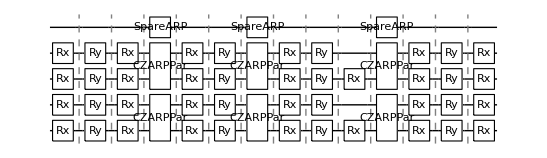

7

```mathematica
ParallelLayerOld={{Subscript[Rx, 0][1.7900363404195456],Subscript[Rx, 1][1.8861283750123876],Subscript[Rx, 2][-1.800315039289523],Subscript[Rx, 3][2.3115020985994335]},{Subscript[Ry, 0][1.4670430226234354],Subscript[Ry, 1][2.5569424815452573],Subscript[Ry, 2][1.2718519181503427],Subscript[Ry, 3][1.5727767539363633]},{Subscript[Rx, 0][-2.484570045260593],Subscript[Rx, 1][2.509739273829867],Subscript[Rx, 2][-1.008282709541314],Subscript[Rx, 3][-1.2363677858856938]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][2.2117766315814684],Subscript[Rx, 1][0.37769195058327476],Subscript[Rx, 2][2.1838751507695022],Subscript[Rx, 3][0.08047640854824678]},{Subscript[Ry, 0][3.141592653589793],Subscript[Ry, 1][-1.5707963267948966],Subscript[Ry, 2][3.141592653589793],Subscript[Ry, 3][-1.5707963267948968]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][1.2196690476758798],Subscript[Rx, 1][1.5707963267948966],Subscript[Rx, 2][1.8392828206538194],Subscript[Rx, 3][1.5707963267948966]},{Subscript[Ry, 0][1.5707963267948966],Subscript[Ry, 1][1.5707963267948966],Subscript[Ry, 2][1.5707963267948963],Subscript[Ry, 3][1.5707963267948966]},{Subscript[Rx, 0][-1.5707963267948966],Subscript[Rx, 2][-1.5707963267948966]},{Subscript[CZARPPar, 0,1],Subscript[CZARPPar, 2,3],Subscript[SpareARP, 4]},{Subscript[Rx, 0][1.672338589319752],Subscript[Rx, 1][0.6372743114520656],Subscript[Rx, 2][-1.9660531239738477],Subscript[Rx, 3][-2.488052553022853]},{Subscript[Ry, 0][0.7530375632248356],Subscript[Ry, 1][2.3118928078424674],Subscript[Ry, 2][1.7008475322590162],Subscript[Ry, 3][2.485809942797934]},{Subscript[Rx, 0][-2.653585823624521],Subscript[Rx, 1][-2.1244988388046213],Subscript[Rx, 2][-2.552028929075849],Subscript[Rx, 3][2.1499700971619315]}}
DrawCircuit[%]
```

```mathematica
{{0,{Subscript[Rx, 0][1.7900363404195456],Subscript[Rx, 1][1.8861283750123876],Subscript[Rx, 2][-1.800315039289523],Subscript[Rx, 3][2.3115020985994335]}},{2.3115020985994335,{Subscript[Ry, 0][1.4670430226234354],Subscript[Ry, 1][2.5569424815452573],Subscript[Ry, 2][1.2718519181503427],Subscript[Ry, 3][1.5727767539363633]}},{4.868444580144691,{Subscript[Rx, 0][-2.484570045260593],Subscript[Rx, 1][2.509739273829867],Subscript[Rx, 2][-1.008282709541314],Subscript[Rx, 3][-1.2363677858856938]}},{7.378183853974558,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{7.378183853974558,{Subscript[Rx, 0][2.2117766315814684],Subscript[Rx, 1][0.37769195058327476],Subscript[Rx, 2][2.1838751507695022],Subscript[Rx, 3][0.08047640854824678]}},{9.589960485556027,{Subscript[Ry, 0][3.141592653589793],Subscript[Ry, 1][-1.5707963267948966],Subscript[Ry, 2][3.141592653589793],Subscript[Ry, 3][-1.5707963267948968]}},{12.73155313914582,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{12.73155313914582,{Subscript[Rx, 0][1.2196690476758798],Subscript[Rx, 1][1.5707963267948966],Subscript[Rx, 2][1.8392828206538194],Subscript[Rx, 3][1.5707963267948966]}},{14.57083595979964,{Subscript[Ry, 0][1.5707963267948966],Subscript[Ry, 1][1.5707963267948966],Subscript[Ry, 2][1.5707963267948963],Subscript[Ry, 3][1.5707963267948966]}},{16.141632286594536,{Subscript[Rx, 0][-1.5707963267948966],Subscript[Rx, 2][-1.5707963267948966]}},{17.712428613389434,{Subscript[U, 0,1][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[U, 2,3][{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}}],Subscript[Id, 4]}},{17.712428613389434,{Subscript[Rx, 0][1.672338589319752],Subscript[Rx, 1][0.6372743114520656],Subscript[Rx, 2][-1.9660531239738477],Subscript[Rx, 3][-2.488052553022853]}},{20.20048116641229,{Subscript[Ry, 0][0.7530375632248356],Subscript[Ry, 1][2.3118928078424674],Subscript[Ry, 2][1.7008475322590162],Subscript[Ry, 3][2.485809942797934]}},{22.686291109210224,{Subscript[Rx, 0][-2.653585823624521],Subscript[Rx, 1][-2.1244988388046213],Subscript[Rx, 2][-2.552028929075849],Subscript[Rx, 3][2.1499700971619315]}},{25.339876932834745,{}}}
```

```mathematica
InsertCircuitNoise[{Subscript[SpareARP, 0]},RydDev,ReplaceAliases->True]
```

{{0,{Deph_0[4.36241×10^-7]},{Deph_0[0.],Deph_1[0.],Deph_2[0.],Deph_3[0.],Deph_4[0.],Deph_5[0.],Deph_6[0.],Deph_7[0.],Deph_8[0.]}},{0,{},{}}}

5

{0,1,2,3,4}

1

General::munfl: Exp[-671141.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{Rx_0[-1.39898],Rx_1[2.35008],Rx_2[-0.261282],Rx_3[-1.28709]},{Ry_0[1.62867],Ry_1[0.941758],Ry_2[0.792034],Ry_3[0.936994]},{Rx_0[1.45827],Rx_1[-0.467045],Rx_2[2.46382],Rx_3[-2.28206]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.96106],Rx_1[0.231888],Rx_2[2.25239],Rx_3[0.0229398]},{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.81862],Rx_1[1.5708],Rx_2[1.33254],Rx_3[1.5708]},{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]},{Rx_0[-1.5708],Rx_2[-1.5708]},{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]},{Rx_0[1.13586],Rx_1[-1.30951],Rx_2[-1.54958],Rx_3[3.07285]},{Ry_0[1.30701],Ry_1[1.57267],Ry_2[2.11492],Ry_3[2.72632]},{Rx_0[-0.417784],Rx_1[2.88766],Rx_2[1.0991],Rx_3[-1.01639]}}

{{0,{Rx_0[-1.39898],Rx_1[2.35008],Rx_2[-0.261282],Rx_3[-1.28709]}},{2.35008,{Ry_0[1.62867],Ry_1[0.941758],Ry_2[0.792034],Ry_3[0.936994]}},{3.97875,{Rx_0[1.45827],Rx_1[-0.467045],Rx_2[2.46382],Rx_3[-2.28206]}},{6.44257,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{7.74257,{Rx_0[1.96106],Rx_1[0.231888],Rx_2[2.25239],Rx_3[0.0229398]}},{9.99496,{Ry_0[3.14159],Ry_1[-1.5708],Ry_2[3.14159],Ry_3[-1.5708]}},{13.1366,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{14.4366,{Rx_0[1.81862],Rx_1[1.5708],Rx_2[1.33254],Rx_3[1.5708]}},{16.2552,{Ry_0[1.5708],Ry_1[1.5708],Ry_2[1.5708],Ry_3[1.5708]}},{17.826,{Rx_0[-1.5708],Rx_2[-1.5708]}},{19.3968,{CZARP_(0,1),CZARP_(2,3),Wait_4[0.5]}},{20.6968,{Rx_0[1.13586],Rx_1[-1.30951],Rx_2[-1.54958],Rx_3[3.07285]}},{23.7696,{Ry_0[1.30701],Ry_1[1.57267],Ry_2[2.11492],Ry_3[2.72632]}},{26.4959,{Rx_0[-0.417784],Rx_1[2.88766],Rx_2[1.0991],Rx_3[-1.01639]}},{29.3836,{}}}

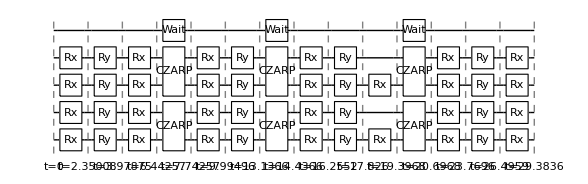

RydbergHub[T2]

```mathematica
?InsertCircuitNoise
```

```mathematica
QVLayerARPMove[DataSet_,NQ_,RQs_,i_]:=Join[Table[SU4GateARPMove[DataSet[[n+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];
```

```mathematica
SU4GateARPMove[data[[1]],0,1]
SU4GateARPMove[data[[4]],0,1]
```

{{Rx_0[-1.39898],Ry_0[1.62867],Rx_0[1.45827],Rx_1[2.35008],Ry_1[0.941758],Rx_1[-0.467045]},{CZARP_(0,1)},{Rx_0[1.96106],Ry_0[3.14159],Rx_1[0.231888],Ry_1[-1.5708]},{CZARP_(0,1)},{Rx_0[1.81862],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708]},{CZARP_(0,1)},{Rx_0[1.13586],Ry_0[1.30701],Rx_0[-0.417784],Rx_1[-1.30951],Ry_1[1.57267],Rx_1[2.88766]}}

```mathematica
?Join
```

```mathematica
?GetCircuitSchedule
```

```mathematica
?Wait
```

```mathematica
InsertCircuitNoise[CircRydbergHub[{Subscript[Wait, 0][1000]},RydDev,Parallel->True],RydDev]
```

{{0,{Deph_0[0.000335458]},{Deph_0[0.],Deph_1[0.000335458],Deph_2[0.000335458],Deph_3[0.000335458],Deph_4[0.000335458],Deph_5[0.000335458],Deph_6[0.000335458],Deph_7[0.000335458],Deph_8[0.000335458]}},{1000,{},{}}}

{{0,{Rx_0[π],Deph_0[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7]},{Deph_0[0.],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}},{π,{},{Deph_0[-∞],Deph_1[-∞],Deph_2[-∞],Deph_3[-∞],Deph_4[-∞],Deph_5[-∞],Deph_6[-∞],Deph_7[-∞],Deph_8[-∞]}}}

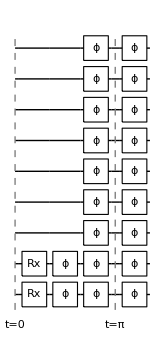

7

7

{Rx_0[π],Deph_0[1.67785×10^-7],Rx_1[π],Deph_1[1.67785×10^-7],Deph_0[0.],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Deph_0[-∞],Deph_1[-∞],Deph_2[-∞],Deph_3[-∞],Deph_4[-∞],Deph_5[-∞],Deph_6[-∞],Deph_7[-∞],Deph_8[-∞]}

ApplyCircuit::error: Circuit contains non-numerical or non-real parameters!

$Failed

```mathematica
Tes=InsertCircuitNoise[GetCircuitSchedule[CircRydbergHub[{Subscript[Rx, 0][Pi],Subscript[Rx, 1][Pi]},RydDev,Parallel->True],RydDev],RydDev]
DrawCircuit[%]
Te=CreateDensityQureg[9]
InitZeroState[Te]
ExtractCircuit[Tes]
ApplyCircuit[Te,ExtractCircuit[Tes]]
```

```mathematica
?GetCircuitSchedule
```

```mathematica
?ApplyCircuit
```

```mathematica
?QuEST`Gate`*
```

```mathematica
CalcCircuitMatrix[{Subscript[Id, 0]}]
```

{{1,0},{0,1}}

PIPropSWAP

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8},Rx_0[-2.66067],Ry_0[2.48921],Rx_0[-1.63876],Rx_1[2.89101],Ry_1[2.25784],Rx_1[1.78126],CZPI_(0,1),Rx_0[2.72886],Ry_0[3.14159],Rx_1[0.379115],Ry_1[-1.5708],CZPI_(0,1),Rx_0[1.42651],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(0,1),Rx_0[3.13812],Ry_0[1.56045],Rx_0[-2.03811],Rx_1[1.67649],Ry_1[1.5903],Rx_1[-1.27163],Rx_2[-2.32899],Ry_2[1.17151],Rx_2[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(2,3),Rx_2[2.56209],Ry_2[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(2,3),Rx_2[1.45211],Ry_2[1.5708],Rx_2[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(2,3),Rx_2[-2.10484],Ry_2[1.24743],Rx_2[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_4[-1.39195],Ry_4[1.57793],Rx_4[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(4,5),Rx_4[2.20863],Ry_4[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(4,5),Rx_4[1.79619],Ry_4[1.5708],Rx_4[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(4,5),Rx_4[0.782167],Ry_4[1.05434],Rx_4[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],Rx_6[0.51528],Ry_6[0.872821],Rx_6[2.06042],Rx_7[-1.87028],Ry_7[2.06996],Rx_7[0.174121],CZPI_(6,7),Rx_6[1.81009],Ry_6[3.14159],Rx_7[0.0219645],Ry_7[-1.5708],CZPI_(6,7),Rx_6[2.14955],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-1.02091],Ry_6[2.04215],Rx_6[-2.33605],Rx_7[0.266953],Ry_7[1.87555],Rx_7[3.09812],Rx_1[-2.32899],Ry_1[1.17151],Rx_1[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(1,3),Rx_1[2.56209],Ry_1[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.45211],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-2.10484],Ry_1[1.24743],Rx_1[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_7[-1.39195],Ry_7[1.57793],Rx_7[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(7,5),Rx_7[2.20863],Ry_7[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.79619],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[0.782167],Ry_7[1.05434],Rx_7[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_0[0.51528],Ry_0[0.872821],Rx_0[2.06042],Rx_4[-1.87028],Ry_4[2.06996],Rx_4[0.174121],CZPI_(0,4),Rx_0[1.81009],Ry_0[3.14159],Rx_4[0.0219645],Ry_4[-1.5708],CZPI_(0,4),Rx_0[2.14955],Ry_0[1.5708],Rx_0[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(0,4),Rx_0[-1.02091],Ry_0[2.04215],Rx_0[-2.33605],Rx_4[0.266953],Ry_4[1.87555],Rx_4[3.09812],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),Rx_8[3.13826],Ry_8[0.218841],Rx_8[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(8,2),Rx_8[2.2051],Ry_8[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(8,2),Rx_8[1.81756],Ry_8[1.5708],Rx_8[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(8,2),Rx_8[-0.481446],Ry_8[1.01943],Rx_8[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.39195],Ry_5[1.57793],Rx_5[1.49418],Rx_7[-0.370106],Ry_7[1.52717],Rx_7[2.2789],CZPI_(5,7),Rx_5[2.20863],Ry_5[3.14159],Rx_7[0.0186374],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.79619],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[0.782167],Ry_5[1.05434],Rx_5[1.81347],Rx_7[2.5813],Ry_7[2.27545],Rx_7[2.29162],Rx_3[0.51528],Ry_3[0.872821],Rx_3[2.06042],Rx_1[-1.87028],Ry_1[2.06996],Rx_1[0.174121],CZPI_(3,1),Rx_3[1.81009],Ry_3[3.14159],Rx_1[0.0219645],Ry_1[-1.5708],CZPI_(3,1),Rx_3[2.14955],Ry_3[1.5708],Rx_3[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(3,1),Rx_3[-1.02091],Ry_3[2.04215],Rx_3[-2.33605],Rx_1[0.266953],Ry_1[1.87555],Rx_1[3.09812],SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[3.13826],Ry_2[0.218841],Rx_2[-1.04983],Rx_6[-2.95012],Ry_6[1.43387],Rx_6[-2.41859],CZPI_(2,6),Rx_2[2.2051],Ry_2[3.14159],Rx_6[0.271485],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.81756],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-0.481446],Ry_2[1.01943],Rx_2[0.573931],Rx_6[3.08096],Ry_6[1.17489],Rx_6[-2.93058],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-1.55441],Ry_8[1.68038],Rx_8[-2.79064],Rx_0[3.0472],Ry_0[0.987925],Rx_0[1.73215],CZPI_(8,0),Rx_8[2.3045],Ry_8[3.14159],Rx_0[0.0593244],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.62638],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.43119],Ry_8[0.814166],Rx_8[-2.70264],Rx_0[-1.17814],Ry_0[1.96067],Rx_0[-0.0164073],Rx_8[0.51528],Ry_8[0.872821],Rx_8[2.06042],Rx_0[-1.87028],Ry_0[2.06996],Rx_0[0.174121],CZPI_(8,0),Rx_8[1.81009],Ry_8[3.14159],Rx_0[0.0219645],Ry_0[-1.5708],CZPI_(8,0),Rx_8[2.14955],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.02091],Ry_8[2.04215],Rx_8[-2.33605],Rx_0[0.266953],Ry_0[1.87555],Rx_0[3.09812],Rx_4[3.13826],Ry_4[0.218841],Rx_4[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(4,2),Rx_4[2.2051],Ry_4[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(4,2),Rx_4[1.81756],Ry_4[1.5708],Rx_4[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(4,2),Rx_4[-0.481446],Ry_4[1.01943],Rx_4[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.55441],Ry_5[1.68038],Rx_5[-2.79064],Rx_7[3.0472],Ry_7[0.987925],Rx_7[1.73215],CZPI_(5,7),Rx_5[2.3045],Ry_5[3.14159],Rx_7[0.0593244],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.62638],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[-1.43119],Ry_5[0.814166],Rx_5[-2.70264],Rx_7[-1.17814],Ry_7[1.96067],Rx_7[-0.0164073],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),SWAPDCPIRL_(4,6),SWAPLoc_(4,6),SWAPDCPIRL_(8,6),SWAPLoc_(8,6),Rx_6[-3.01975],Ry_6[1.29558],Rx_6[-2.24939],Rx_3[-2.02749],Ry_3[0.999609],Rx_3[-0.987031],CZPI_(6,3),Rx_6[2.64453],Ry_6[3.14159],Rx_3[0.065984],Ry_3[-1.5708],CZPI_(6,3),Rx_6[1.76505],Ry_6[1.5708],Rx_6[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(6,3),Rx_6[0.720167],Ry_6[1.9509],Rx_6[0.865704],Rx_3[0.883284],Ry_3[2.23981],Rx_3[-1.17633],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),SWAPDCPIRL_(6,4),SWAPLoc_(6,4),Rx_3[3.13826],Ry_3[0.218841],Rx_3[-1.04983],Rx_4[-2.95012],Ry_4[1.43387],Rx_4[-2.41859],CZPI_(3,4),Rx_3[2.2051],Ry_3[3.14159],Rx_4[0.271485],Ry_4[-1.5708],CZPI_(3,4),Rx_3[1.81756],Ry_3[1.5708],Rx_3[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(3,4),Rx_3[-0.481446],Ry_3[1.01943],Rx_3[0.573931],Rx_4[3.08096],Ry_4[1.17489],Rx_4[-2.93058],SWAPDCPIRL_(2,8),SWAPLoc_(8,2),Rx_2[-1.55441],Ry_2[1.68038],Rx_2[-2.79064],Rx_6[3.0472],Ry_6[0.987925],Rx_6[1.73215],CZPI_(2,6),Rx_2[2.3045],Ry_2[3.14159],Rx_6[0.0593244],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.62638],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.43119],Ry_2[0.814166],Rx_2[-2.70264],Rx_6[-1.17814],Ry_6[1.96067],Rx_6[-0.0164073],SWAPDCPIRL_(7,5),SWAPLoc_(5,7),SWAPDCPIRL_(7,3),SWAPLoc_(3,7),Rx_1[-3.01975],Ry_1[1.29558],Rx_1[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(1,7),Rx_1[2.64453],Ry_1[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(1,7),Rx_1[1.76505],Ry_1[1.5708],Rx_1[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(1,7),Rx_1[0.720167],Ry_1[1.9509],Rx_1[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-0.489465],Ry_8[0.0900604],Rx_8[-2.76932],Rx_0[2.82771],Ry_0[1.33036],Rx_0[3.05406],CZPI_(8,0),Rx_8[2.29677],Ry_8[3.14159],Rx_0[0.0569514],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.97364],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-2.2952],Ry_8[0.809808],Rx_8[2.43034],Rx_0[-0.397025],Ry_0[1.23985],Rx_0[2.57758],Rx_3[-1.55441],Ry_3[1.68038],Rx_3[-2.79064],Rx_5[3.0472],Ry_5[0.987925],Rx_5[1.73215],CZPI_(3,5),Rx_3[2.3045],Ry_3[3.14159],Rx_5[0.0593244],Ry_5[-1.5708],CZPI_(3,5),Rx_3[1.62638],Ry_3[1.5708],Rx_3[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(3,5),Rx_3[-1.43119],Ry_3[0.814166],Rx_3[-2.70264],Rx_5[-1.17814],Ry_5[1.96067],Rx_5[-0.0164073],SWAPDCPIRL_(1,7),SWAPLoc_(1,7),Rx_0[-3.01975],Ry_0[1.29558],Rx_0[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(0,7),Rx_0[2.64453],Ry_0[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.76505],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[0.720167],Ry_0[1.9509],Rx_0[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_8[2.82771],Ry_8[1.33036],Rx_8[3.05406],CZPI_(6,8),Rx_6[2.29677],Ry_6[3.14159],Rx_8[0.0569514],Ry_8[-1.5708],CZPI_(6,8),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(6,8),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_8[-0.397025],Ry_8[1.23985],Rx_8[2.57758],SWAPDCPIRL_(4,2),SWAPLoc_(4,2),SWAPDCPIRL_(6,2),SWAPLoc_(6,2),SWAPDCPIRL_(8,2),SWAPLoc_(8,2),Rx_2[0.375278],Ry_2[0.478591],Rx_2[-1.19936],Rx_1[2.39762],Ry_1[0.736948],Rx_1[0.814127],CZPI_(2,1),Rx_2[2.64681],Ry_2[3.14159],Rx_1[0.133942],Ry_1[-1.5708],CZPI_(2,1),Rx_2[1.63012],Ry_2[1.5708],Rx_2[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(2,1),Rx_2[-0.155377],Ry_2[1.7214],Rx_2[0.742619],Rx_1[1.27734],Ry_1[1.8495],Rx_1[-2.62415],SWAPDCPIRL_(4,6),SWAPLoc_(6,4),Rx_4[-3.01975],Ry_4[1.29558],Rx_4[-2.24939],Rx_8[-2.02749],Ry_8[0.999609],Rx_8[-0.987031],CZPI_(4,8),Rx_4[2.64453],Ry_4[3.14159],Rx_8[0.065984],Ry_8[-1.5708],CZPI_(4,8),Rx_4[1.76505],Ry_4[1.5708],Rx_4[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(4,8),Rx_4[0.720167],Ry_4[1.9509],Rx_4[0.865704],Rx_8[0.883284],Ry_8[2.23981],Rx_8[-1.17633],SWAPDCPIRL_(1,3),SWAPLoc_(1,3),SWAPDCPIRL_(7,3),SWAPLoc_(7,3),Rx_0[-0.489465],Ry_0[0.0900604],Rx_0[-2.76932],Rx_3[2.82771],Ry_3[1.33036],Rx_3[3.05406],CZPI_(0,3),Rx_0[2.29677],Ry_0[3.14159],Rx_3[0.0569514],Ry_3[-1.5708],CZPI_(0,3),Rx_0[1.97364],Ry_0[1.5708],Rx_0[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(0,3),Rx_0[-2.2952],Ry_0[0.809808],Rx_0[2.43034],Rx_3[-0.397025],Ry_3[1.23985],Rx_3[2.57758],SWAPDCPIRL_(5,1),SWAPLoc_(1,5),Rx_7[0.375278],Ry_7[0.478591],Rx_7[-1.19936],Rx_5[2.39762],Ry_5[0.736948],Rx_5[0.814127],CZPI_(7,5),Rx_7[2.64681],Ry_7[3.14159],Rx_5[0.133942],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.63012],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[-0.155377],Ry_7[1.7214],Rx_7[0.742619],Rx_5[1.27734],Ry_5[1.8495],Rx_5[-2.62415],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_6[-0.681977],Ry_6[0.308252],Rx_6[0.123506],CZPI_(2,6),Rx_2[2.20709],Ry_2[3.14159],Rx_6[0.0196703],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_6[1.83724],Ry_6[1.71253],Rx_6[0.166782],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_7[2.82771],Ry_7[1.33036],Rx_7[3.05406],CZPI_(6,7),Rx_6[2.29677],Ry_6[3.14159],Rx_7[0.0569514],Ry_7[-1.5708],CZPI_(6,7),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_7[-0.397025],Ry_7[1.23985],Rx_7[2.57758],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),Rx_1[0.375278],Ry_1[0.478591],Rx_1[-1.19936],Rx_4[2.39762],Ry_4[0.736948],Rx_4[0.814127],CZPI_(1,4),Rx_1[2.64681],Ry_1[3.14159],Rx_4[0.133942],Ry_4[-1.5708],CZPI_(1,4),Rx_1[1.63012],Ry_1[1.5708],Rx_1[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(1,4),Rx_1[-0.155377],Ry_1[1.7214],Rx_1[0.742619],Rx_4[1.27734],Ry_4[1.8495],Rx_4[-2.62415],Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_5[-0.681977],Ry_5[0.308252],Rx_5[0.123506],CZPI_(2,5),Rx_2[2.20709],Ry_2[3.14159],Rx_5[0.0196703],Ry_5[-1.5708],CZPI_(2,5),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(2,5),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_5[1.83724],Ry_5[1.71253],Rx_5[0.166782],Rx_3[-2.17134],Ry_3[1.83016],Rx_3[-2.94644],Rx_0[-1.68107],Ry_0[2.11689],Rx_0[-1.19433],CZPI_(3,0),Rx_3[2.39231],Ry_3[3.14159],Rx_0[0.416043],Ry_0[-1.5708],CZPI_(3,0),Rx_3[1.36036],Ry_3[1.5708],Rx_3[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(3,0),Rx_3[-2.14897],Ry_3[1.0164],Rx_3[-1.04764],Rx_0[-1.53464],Ry_0[1.19577],Rx_0[-2.60027],Rx_5[0.375278],Ry_5[0.478591],Rx_5[-1.19936],Rx_2[2.39762],Ry_2[0.736948],Rx_2[0.814127],CZPI_(5,2),Rx_5[2.64681],Ry_5[3.14159],Rx_2[0.133942],Ry_2[-1.5708],CZPI_(5,2),Rx_5[1.63012],Ry_5[1.5708],Rx_5[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(5,2),Rx_5[-0.155377],Ry_5[1.7214],Rx_5[0.742619],Rx_2[1.27734],Ry_2[1.8495],Rx_2[-2.62415],SWAPDCPIRL_(3,7),SWAPLoc_(3,7),Rx_0[-2.13517],Ry_0[2.8561],Rx_0[-1.06381],Rx_7[-0.681977],Ry_7[0.308252],Rx_7[0.123506],CZPI_(0,7),Rx_0[2.20709],Ry_0[3.14159],Rx_7[0.0196703],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.9643],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[-1.4508],Ry_0[2.32453],Rx_0[-0.323213],Rx_7[1.83724],Ry_7[1.71253],Rx_7[0.166782],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_4[-2.17134],Ry_4[1.83016],Rx_4[-2.94644],Rx_6[-1.68107],Ry_6[2.11689],Rx_6[-1.19433],CZPI_(4,6),Rx_4[2.39231],Ry_4[3.14159],Rx_6[0.416043],Ry_6[-1.5708],CZPI_(4,6),Rx_4[1.36036],Ry_4[1.5708],Rx_4[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(4,6),Rx_4[-2.14897],Ry_4[1.0164],Rx_4[-1.04764],Rx_6[-1.53464],Ry_6[1.19577],Rx_6[-2.60027],SWAPDCPIRL_(1,5),SWAPLoc_(5,1),Rx_1[1.05776],Ry_1[0.436939],Rx_1[-2.45802],Rx_3[1.74813],Ry_3[2.17212],Rx_3[2.02089],CZPI_(1,3),Rx_1[2.18474],Ry_1[3.14159],Rx_3[0.0251886],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.06059],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-0.539465],Ry_1[1.12057],Rx_1[-3.02557],Rx_3[2.30356],Ry_3[0.356693],Rx_3[2.00006]}

{Layer,7,128,128}

PIPropSWAP

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8},Rx_0[-2.66067],Ry_0[2.48921],Rx_0[-1.63876],Rx_1[2.89101],Ry_1[2.25784],Rx_1[1.78126],CZPI_(0,1),Rx_0[2.72886],Ry_0[3.14159],Rx_1[0.379115],Ry_1[-1.5708],CZPI_(0,1),Rx_0[1.42651],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(0,1),Rx_0[3.13812],Ry_0[1.56045],Rx_0[-2.03811],Rx_1[1.67649],Ry_1[1.5903],Rx_1[-1.27163],Rx_2[-2.32899],Ry_2[1.17151],Rx_2[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(2,3),Rx_2[2.56209],Ry_2[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(2,3),Rx_2[1.45211],Ry_2[1.5708],Rx_2[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(2,3),Rx_2[-2.10484],Ry_2[1.24743],Rx_2[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_4[-1.39195],Ry_4[1.57793],Rx_4[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(4,5),Rx_4[2.20863],Ry_4[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(4,5),Rx_4[1.79619],Ry_4[1.5708],Rx_4[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(4,5),Rx_4[0.782167],Ry_4[1.05434],Rx_4[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],Rx_6[0.51528],Ry_6[0.872821],Rx_6[2.06042],Rx_7[-1.87028],Ry_7[2.06996],Rx_7[0.174121],CZPI_(6,7),Rx_6[1.81009],Ry_6[3.14159],Rx_7[0.0219645],Ry_7[-1.5708],CZPI_(6,7),Rx_6[2.14955],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-1.02091],Ry_6[2.04215],Rx_6[-2.33605],Rx_7[0.266953],Ry_7[1.87555],Rx_7[3.09812],Rx_1[-2.32899],Ry_1[1.17151],Rx_1[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(1,3),Rx_1[2.56209],Ry_1[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.45211],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-2.10484],Ry_1[1.24743],Rx_1[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_7[-1.39195],Ry_7[1.57793],Rx_7[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(7,5),Rx_7[2.20863],Ry_7[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.79619],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[0.782167],Ry_7[1.05434],Rx_7[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_0[0.51528],Ry_0[0.872821],Rx_0[2.06042],Rx_4[-1.87028],Ry_4[2.06996],Rx_4[0.174121],CZPI_(0,4),Rx_0[1.81009],Ry_0[3.14159],Rx_4[0.0219645],Ry_4[-1.5708],CZPI_(0,4),Rx_0[2.14955],Ry_0[1.5708],Rx_0[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(0,4),Rx_0[-1.02091],Ry_0[2.04215],Rx_0[-2.33605],Rx_4[0.266953],Ry_4[1.87555],Rx_4[3.09812],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),Rx_8[3.13826],Ry_8[0.218841],Rx_8[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(8,2),Rx_8[2.2051],Ry_8[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(8,2),Rx_8[1.81756],Ry_8[1.5708],Rx_8[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(8,2),Rx_8[-0.481446],Ry_8[1.01943],Rx_8[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.39195],Ry_5[1.57793],Rx_5[1.49418],Rx_7[-0.370106],Ry_7[1.52717],Rx_7[2.2789],CZPI_(5,7),Rx_5[2.20863],Ry_5[3.14159],Rx_7[0.0186374],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.79619],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[0.782167],Ry_5[1.05434],Rx_5[1.81347],Rx_7[2.5813],Ry_7[2.27545],Rx_7[2.29162],Rx_3[0.51528],Ry_3[0.872821],Rx_3[2.06042],Rx_1[-1.87028],Ry_1[2.06996],Rx_1[0.174121],CZPI_(3,1),Rx_3[1.81009],Ry_3[3.14159],Rx_1[0.0219645],Ry_1[-1.5708],CZPI_(3,1),Rx_3[2.14955],Ry_3[1.5708],Rx_3[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(3,1),Rx_3[-1.02091],Ry_3[2.04215],Rx_3[-2.33605],Rx_1[0.266953],Ry_1[1.87555],Rx_1[3.09812],SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[3.13826],Ry_2[0.218841],Rx_2[-1.04983],Rx_6[-2.95012],Ry_6[1.43387],Rx_6[-2.41859],CZPI_(2,6),Rx_2[2.2051],Ry_2[3.14159],Rx_6[0.271485],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.81756],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-0.481446],Ry_2[1.01943],Rx_2[0.573931],Rx_6[3.08096],Ry_6[1.17489],Rx_6[-2.93058],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-1.55441],Ry_8[1.68038],Rx_8[-2.79064],Rx_0[3.0472],Ry_0[0.987925],Rx_0[1.73215],CZPI_(8,0),Rx_8[2.3045],Ry_8[3.14159],Rx_0[0.0593244],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.62638],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.43119],Ry_8[0.814166],Rx_8[-2.70264],Rx_0[-1.17814],Ry_0[1.96067],Rx_0[-0.0164073],Rx_8[0.51528],Ry_8[0.872821],Rx_8[2.06042],Rx_0[-1.87028],Ry_0[2.06996],Rx_0[0.174121],CZPI_(8,0),Rx_8[1.81009],Ry_8[3.14159],Rx_0[0.0219645],Ry_0[-1.5708],CZPI_(8,0),Rx_8[2.14955],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.02091],Ry_8[2.04215],Rx_8[-2.33605],Rx_0[0.266953],Ry_0[1.87555],Rx_0[3.09812],Rx_4[3.13826],Ry_4[0.218841],Rx_4[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(4,2),Rx_4[2.2051],Ry_4[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(4,2),Rx_4[1.81756],Ry_4[1.5708],Rx_4[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(4,2),Rx_4[-0.481446],Ry_4[1.01943],Rx_4[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.55441],Ry_5[1.68038],Rx_5[-2.79064],Rx_7[3.0472],Ry_7[0.987925],Rx_7[1.73215],CZPI_(5,7),Rx_5[2.3045],Ry_5[3.14159],Rx_7[0.0593244],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.62638],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[-1.43119],Ry_5[0.814166],Rx_5[-2.70264],Rx_7[-1.17814],Ry_7[1.96067],Rx_7[-0.0164073],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),SWAPDCPIRL_(4,6),SWAPLoc_(4,6),SWAPDCPIRL_(8,6),SWAPLoc_(8,6),Rx_6[-3.01975],Ry_6[1.29558],Rx_6[-2.24939],Rx_3[-2.02749],Ry_3[0.999609],Rx_3[-0.987031],CZPI_(6,3),Rx_6[2.64453],Ry_6[3.14159],Rx_3[0.065984],Ry_3[-1.5708],CZPI_(6,3),Rx_6[1.76505],Ry_6[1.5708],Rx_6[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(6,3),Rx_6[0.720167],Ry_6[1.9509],Rx_6[0.865704],Rx_3[0.883284],Ry_3[2.23981],Rx_3[-1.17633],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),SWAPDCPIRL_(6,4),SWAPLoc_(6,4),Rx_3[3.13826],Ry_3[0.218841],Rx_3[-1.04983],Rx_4[-2.95012],Ry_4[1.43387],Rx_4[-2.41859],CZPI_(3,4),Rx_3[2.2051],Ry_3[3.14159],Rx_4[0.271485],Ry_4[-1.5708],CZPI_(3,4),Rx_3[1.81756],Ry_3[1.5708],Rx_3[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(3,4),Rx_3[-0.481446],Ry_3[1.01943],Rx_3[0.573931],Rx_4[3.08096],Ry_4[1.17489],Rx_4[-2.93058],SWAPDCPIRL_(2,8),SWAPLoc_(8,2),Rx_2[-1.55441],Ry_2[1.68038],Rx_2[-2.79064],Rx_6[3.0472],Ry_6[0.987925],Rx_6[1.73215],CZPI_(2,6),Rx_2[2.3045],Ry_2[3.14159],Rx_6[0.0593244],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.62638],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.43119],Ry_2[0.814166],Rx_2[-2.70264],Rx_6[-1.17814],Ry_6[1.96067],Rx_6[-0.0164073],SWAPDCPIRL_(7,5),SWAPLoc_(5,7),SWAPDCPIRL_(7,3),SWAPLoc_(3,7),Rx_1[-3.01975],Ry_1[1.29558],Rx_1[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(1,7),Rx_1[2.64453],Ry_1[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(1,7),Rx_1[1.76505],Ry_1[1.5708],Rx_1[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(1,7),Rx_1[0.720167],Ry_1[1.9509],Rx_1[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-0.489465],Ry_8[0.0900604],Rx_8[-2.76932],Rx_0[2.82771],Ry_0[1.33036],Rx_0[3.05406],CZPI_(8,0),Rx_8[2.29677],Ry_8[3.14159],Rx_0[0.0569514],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.97364],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-2.2952],Ry_8[0.809808],Rx_8[2.43034],Rx_0[-0.397025],Ry_0[1.23985],Rx_0[2.57758],Rx_3[-1.55441],Ry_3[1.68038],Rx_3[-2.79064],Rx_5[3.0472],Ry_5[0.987925],Rx_5[1.73215],CZPI_(3,5),Rx_3[2.3045],Ry_3[3.14159],Rx_5[0.0593244],Ry_5[-1.5708],CZPI_(3,5),Rx_3[1.62638],Ry_3[1.5708],Rx_3[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(3,5),Rx_3[-1.43119],Ry_3[0.814166],Rx_3[-2.70264],Rx_5[-1.17814],Ry_5[1.96067],Rx_5[-0.0164073],SWAPDCPIRL_(1,7),SWAPLoc_(1,7),Rx_0[-3.01975],Ry_0[1.29558],Rx_0[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(0,7),Rx_0[2.64453],Ry_0[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.76505],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[0.720167],Ry_0[1.9509],Rx_0[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_8[2.82771],Ry_8[1.33036],Rx_8[3.05406],CZPI_(6,8),Rx_6[2.29677],Ry_6[3.14159],Rx_8[0.0569514],Ry_8[-1.5708],CZPI_(6,8),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(6,8),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_8[-0.397025],Ry_8[1.23985],Rx_8[2.57758],SWAPDCPIRL_(4,2),SWAPLoc_(4,2),SWAPDCPIRL_(6,2),SWAPLoc_(6,2),SWAPDCPIRL_(8,2),SWAPLoc_(8,2),Rx_2[0.375278],Ry_2[0.478591],Rx_2[-1.19936],Rx_1[2.39762],Ry_1[0.736948],Rx_1[0.814127],CZPI_(2,1),Rx_2[2.64681],Ry_2[3.14159],Rx_1[0.133942],Ry_1[-1.5708],CZPI_(2,1),Rx_2[1.63012],Ry_2[1.5708],Rx_2[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(2,1),Rx_2[-0.155377],Ry_2[1.7214],Rx_2[0.742619],Rx_1[1.27734],Ry_1[1.8495],Rx_1[-2.62415],SWAPDCPIRL_(4,6),SWAPLoc_(6,4),Rx_4[-3.01975],Ry_4[1.29558],Rx_4[-2.24939],Rx_8[-2.02749],Ry_8[0.999609],Rx_8[-0.987031],CZPI_(4,8),Rx_4[2.64453],Ry_4[3.14159],Rx_8[0.065984],Ry_8[-1.5708],CZPI_(4,8),Rx_4[1.76505],Ry_4[1.5708],Rx_4[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(4,8),Rx_4[0.720167],Ry_4[1.9509],Rx_4[0.865704],Rx_8[0.883284],Ry_8[2.23981],Rx_8[-1.17633],SWAPDCPIRL_(1,3),SWAPLoc_(1,3),SWAPDCPIRL_(7,3),SWAPLoc_(7,3),Rx_0[-0.489465],Ry_0[0.0900604],Rx_0[-2.76932],Rx_3[2.82771],Ry_3[1.33036],Rx_3[3.05406],CZPI_(0,3),Rx_0[2.29677],Ry_0[3.14159],Rx_3[0.0569514],Ry_3[-1.5708],CZPI_(0,3),Rx_0[1.97364],Ry_0[1.5708],Rx_0[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(0,3),Rx_0[-2.2952],Ry_0[0.809808],Rx_0[2.43034],Rx_3[-0.397025],Ry_3[1.23985],Rx_3[2.57758],SWAPDCPIRL_(5,1),SWAPLoc_(1,5),Rx_7[0.375278],Ry_7[0.478591],Rx_7[-1.19936],Rx_5[2.39762],Ry_5[0.736948],Rx_5[0.814127],CZPI_(7,5),Rx_7[2.64681],Ry_7[3.14159],Rx_5[0.133942],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.63012],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[-0.155377],Ry_7[1.7214],Rx_7[0.742619],Rx_5[1.27734],Ry_5[1.8495],Rx_5[-2.62415],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_6[-0.681977],Ry_6[0.308252],Rx_6[0.123506],CZPI_(2,6),Rx_2[2.20709],Ry_2[3.14159],Rx_6[0.0196703],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_6[1.83724],Ry_6[1.71253],Rx_6[0.166782],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_7[2.82771],Ry_7[1.33036],Rx_7[3.05406],CZPI_(6,7),Rx_6[2.29677],Ry_6[3.14159],Rx_7[0.0569514],Ry_7[-1.5708],CZPI_(6,7),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_7[-0.397025],Ry_7[1.23985],Rx_7[2.57758],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),Rx_1[0.375278],Ry_1[0.478591],Rx_1[-1.19936],Rx_4[2.39762],Ry_4[0.736948],Rx_4[0.814127],CZPI_(1,4),Rx_1[2.64681],Ry_1[3.14159],Rx_4[0.133942],Ry_4[-1.5708],CZPI_(1,4),Rx_1[1.63012],Ry_1[1.5708],Rx_1[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(1,4),Rx_1[-0.155377],Ry_1[1.7214],Rx_1[0.742619],Rx_4[1.27734],Ry_4[1.8495],Rx_4[-2.62415],Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_5[-0.681977],Ry_5[0.308252],Rx_5[0.123506],CZPI_(2,5),Rx_2[2.20709],Ry_2[3.14159],Rx_5[0.0196703],Ry_5[-1.5708],CZPI_(2,5),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(2,5),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_5[1.83724],Ry_5[1.71253],Rx_5[0.166782],Rx_3[-2.17134],Ry_3[1.83016],Rx_3[-2.94644],Rx_0[-1.68107],Ry_0[2.11689],Rx_0[-1.19433],CZPI_(3,0),Rx_3[2.39231],Ry_3[3.14159],Rx_0[0.416043],Ry_0[-1.5708],CZPI_(3,0),Rx_3[1.36036],Ry_3[1.5708],Rx_3[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(3,0),Rx_3[-2.14897],Ry_3[1.0164],Rx_3[-1.04764],Rx_0[-1.53464],Ry_0[1.19577],Rx_0[-2.60027],Rx_5[0.375278],Ry_5[0.478591],Rx_5[-1.19936],Rx_2[2.39762],Ry_2[0.736948],Rx_2[0.814127],CZPI_(5,2),Rx_5[2.64681],Ry_5[3.14159],Rx_2[0.133942],Ry_2[-1.5708],CZPI_(5,2),Rx_5[1.63012],Ry_5[1.5708],Rx_5[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(5,2),Rx_5[-0.155377],Ry_5[1.7214],Rx_5[0.742619],Rx_2[1.27734],Ry_2[1.8495],Rx_2[-2.62415],SWAPDCPIRL_(3,7),SWAPLoc_(3,7),Rx_0[-2.13517],Ry_0[2.8561],Rx_0[-1.06381],Rx_7[-0.681977],Ry_7[0.308252],Rx_7[0.123506],CZPI_(0,7),Rx_0[2.20709],Ry_0[3.14159],Rx_7[0.0196703],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.9643],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[-1.4508],Ry_0[2.32453],Rx_0[-0.323213],Rx_7[1.83724],Ry_7[1.71253],Rx_7[0.166782],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_4[-2.17134],Ry_4[1.83016],Rx_4[-2.94644],Rx_6[-1.68107],Ry_6[2.11689],Rx_6[-1.19433],CZPI_(4,6),Rx_4[2.39231],Ry_4[3.14159],Rx_6[0.416043],Ry_6[-1.5708],CZPI_(4,6),Rx_4[1.36036],Ry_4[1.5708],Rx_4[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(4,6),Rx_4[-2.14897],Ry_4[1.0164],Rx_4[-1.04764],Rx_6[-1.53464],Ry_6[1.19577],Rx_6[-2.60027],SWAPDCPIRL_(1,5),SWAPLoc_(5,1),Rx_1[1.05776],Ry_1[0.436939],Rx_1[-2.45802],Rx_3[1.74813],Ry_3[2.17212],Rx_3[2.02089],CZPI_(1,3),Rx_1[2.18474],Ry_1[3.14159],Rx_3[0.0251886],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.06059],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-0.539465],Ry_1[1.12057],Rx_1[-3.02557],Rx_3[2.30356],Ry_3[0.356693],Rx_3[2.00006]}

PIPropSWAP

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8},Rx_0[-2.66067],Ry_0[2.48921],Rx_0[-1.63876],Rx_1[2.89101],Ry_1[2.25784],Rx_1[1.78126],CZPI_(0,1),Rx_0[2.72886],Ry_0[3.14159],Rx_1[0.379115],Ry_1[-1.5708],CZPI_(0,1),Rx_0[1.42651],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(0,1),Rx_0[3.13812],Ry_0[1.56045],Rx_0[-2.03811],Rx_1[1.67649],Ry_1[1.5903],Rx_1[-1.27163],Rx_2[-2.32899],Ry_2[1.17151],Rx_2[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(2,3),Rx_2[2.56209],Ry_2[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(2,3),Rx_2[1.45211],Ry_2[1.5708],Rx_2[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(2,3),Rx_2[-2.10484],Ry_2[1.24743],Rx_2[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_4[-1.39195],Ry_4[1.57793],Rx_4[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(4,5),Rx_4[2.20863],Ry_4[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(4,5),Rx_4[1.79619],Ry_4[1.5708],Rx_4[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(4,5),Rx_4[0.782167],Ry_4[1.05434],Rx_4[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],Rx_6[0.51528],Ry_6[0.872821],Rx_6[2.06042],Rx_7[-1.87028],Ry_7[2.06996],Rx_7[0.174121],CZPI_(6,7),Rx_6[1.81009],Ry_6[3.14159],Rx_7[0.0219645],Ry_7[-1.5708],CZPI_(6,7),Rx_6[2.14955],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-1.02091],Ry_6[2.04215],Rx_6[-2.33605],Rx_7[0.266953],Ry_7[1.87555],Rx_7[3.09812],Rx_1[-2.32899],Ry_1[1.17151],Rx_1[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(1,3),Rx_1[2.56209],Ry_1[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.45211],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-2.10484],Ry_1[1.24743],Rx_1[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_7[-1.39195],Ry_7[1.57793],Rx_7[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(7,5),Rx_7[2.20863],Ry_7[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.79619],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[0.782167],Ry_7[1.05434],Rx_7[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_0[0.51528],Ry_0[0.872821],Rx_0[2.06042],Rx_4[-1.87028],Ry_4[2.06996],Rx_4[0.174121],CZPI_(0,4),Rx_0[1.81009],Ry_0[3.14159],Rx_4[0.0219645],Ry_4[-1.5708],CZPI_(0,4),Rx_0[2.14955],Ry_0[1.5708],Rx_0[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(0,4),Rx_0[-1.02091],Ry_0[2.04215],Rx_0[-2.33605],Rx_4[0.266953],Ry_4[1.87555],Rx_4[3.09812],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),Rx_8[3.13826],Ry_8[0.218841],Rx_8[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(8,2),Rx_8[2.2051],Ry_8[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(8,2),Rx_8[1.81756],Ry_8[1.5708],Rx_8[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(8,2),Rx_8[-0.481446],Ry_8[1.01943],Rx_8[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.39195],Ry_5[1.57793],Rx_5[1.49418],Rx_7[-0.370106],Ry_7[1.52717],Rx_7[2.2789],CZPI_(5,7),Rx_5[2.20863],Ry_5[3.14159],Rx_7[0.0186374],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.79619],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[0.782167],Ry_5[1.05434],Rx_5[1.81347],Rx_7[2.5813],Ry_7[2.27545],Rx_7[2.29162],Rx_3[0.51528],Ry_3[0.872821],Rx_3[2.06042],Rx_1[-1.87028],Ry_1[2.06996],Rx_1[0.174121],CZPI_(3,1),Rx_3[1.81009],Ry_3[3.14159],Rx_1[0.0219645],Ry_1[-1.5708],CZPI_(3,1),Rx_3[2.14955],Ry_3[1.5708],Rx_3[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(3,1),Rx_3[-1.02091],Ry_3[2.04215],Rx_3[-2.33605],Rx_1[0.266953],Ry_1[1.87555],Rx_1[3.09812],SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[3.13826],Ry_2[0.218841],Rx_2[-1.04983],Rx_6[-2.95012],Ry_6[1.43387],Rx_6[-2.41859],CZPI_(2,6),Rx_2[2.2051],Ry_2[3.14159],Rx_6[0.271485],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.81756],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-0.481446],Ry_2[1.01943],Rx_2[0.573931],Rx_6[3.08096],Ry_6[1.17489],Rx_6[-2.93058],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-1.55441],Ry_8[1.68038],Rx_8[-2.79064],Rx_0[3.0472],Ry_0[0.987925],Rx_0[1.73215],CZPI_(8,0),Rx_8[2.3045],Ry_8[3.14159],Rx_0[0.0593244],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.62638],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.43119],Ry_8[0.814166],Rx_8[-2.70264],Rx_0[-1.17814],Ry_0[1.96067],Rx_0[-0.0164073],Rx_8[0.51528],Ry_8[0.872821],Rx_8[2.06042],Rx_0[-1.87028],Ry_0[2.06996],Rx_0[0.174121],CZPI_(8,0),Rx_8[1.81009],Ry_8[3.14159],Rx_0[0.0219645],Ry_0[-1.5708],CZPI_(8,0),Rx_8[2.14955],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.02091],Ry_8[2.04215],Rx_8[-2.33605],Rx_0[0.266953],Ry_0[1.87555],Rx_0[3.09812],Rx_4[3.13826],Ry_4[0.218841],Rx_4[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(4,2),Rx_4[2.2051],Ry_4[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(4,2),Rx_4[1.81756],Ry_4[1.5708],Rx_4[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(4,2),Rx_4[-0.481446],Ry_4[1.01943],Rx_4[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.55441],Ry_5[1.68038],Rx_5[-2.79064],Rx_7[3.0472],Ry_7[0.987925],Rx_7[1.73215],CZPI_(5,7),Rx_5[2.3045],Ry_5[3.14159],Rx_7[0.0593244],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.62638],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[-1.43119],Ry_5[0.814166],Rx_5[-2.70264],Rx_7[-1.17814],Ry_7[1.96067],Rx_7[-0.0164073],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),SWAPDCPIRL_(4,6),SWAPLoc_(4,6),SWAPDCPIRL_(8,6),SWAPLoc_(8,6),Rx_6[-3.01975],Ry_6[1.29558],Rx_6[-2.24939],Rx_3[-2.02749],Ry_3[0.999609],Rx_3[-0.987031],CZPI_(6,3),Rx_6[2.64453],Ry_6[3.14159],Rx_3[0.065984],Ry_3[-1.5708],CZPI_(6,3),Rx_6[1.76505],Ry_6[1.5708],Rx_6[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(6,3),Rx_6[0.720167],Ry_6[1.9509],Rx_6[0.865704],Rx_3[0.883284],Ry_3[2.23981],Rx_3[-1.17633],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),SWAPDCPIRL_(6,4),SWAPLoc_(6,4),Rx_3[3.13826],Ry_3[0.218841],Rx_3[-1.04983],Rx_4[-2.95012],Ry_4[1.43387],Rx_4[-2.41859],CZPI_(3,4),Rx_3[2.2051],Ry_3[3.14159],Rx_4[0.271485],Ry_4[-1.5708],CZPI_(3,4),Rx_3[1.81756],Ry_3[1.5708],Rx_3[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(3,4),Rx_3[-0.481446],Ry_3[1.01943],Rx_3[0.573931],Rx_4[3.08096],Ry_4[1.17489],Rx_4[-2.93058],SWAPDCPIRL_(2,8),SWAPLoc_(8,2),Rx_2[-1.55441],Ry_2[1.68038],Rx_2[-2.79064],Rx_6[3.0472],Ry_6[0.987925],Rx_6[1.73215],CZPI_(2,6),Rx_2[2.3045],Ry_2[3.14159],Rx_6[0.0593244],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.62638],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.43119],Ry_2[0.814166],Rx_2[-2.70264],Rx_6[-1.17814],Ry_6[1.96067],Rx_6[-0.0164073],SWAPDCPIRL_(7,5),SWAPLoc_(5,7),SWAPDCPIRL_(7,3),SWAPLoc_(3,7),Rx_1[-3.01975],Ry_1[1.29558],Rx_1[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(1,7),Rx_1[2.64453],Ry_1[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(1,7),Rx_1[1.76505],Ry_1[1.5708],Rx_1[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(1,7),Rx_1[0.720167],Ry_1[1.9509],Rx_1[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-0.489465],Ry_8[0.0900604],Rx_8[-2.76932],Rx_0[2.82771],Ry_0[1.33036],Rx_0[3.05406],CZPI_(8,0),Rx_8[2.29677],Ry_8[3.14159],Rx_0[0.0569514],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.97364],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-2.2952],Ry_8[0.809808],Rx_8[2.43034],Rx_0[-0.397025],Ry_0[1.23985],Rx_0[2.57758],Rx_3[-1.55441],Ry_3[1.68038],Rx_3[-2.79064],Rx_5[3.0472],Ry_5[0.987925],Rx_5[1.73215],CZPI_(3,5),Rx_3[2.3045],Ry_3[3.14159],Rx_5[0.0593244],Ry_5[-1.5708],CZPI_(3,5),Rx_3[1.62638],Ry_3[1.5708],Rx_3[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(3,5),Rx_3[-1.43119],Ry_3[0.814166],Rx_3[-2.70264],Rx_5[-1.17814],Ry_5[1.96067],Rx_5[-0.0164073],SWAPDCPIRL_(1,7),SWAPLoc_(1,7),Rx_0[-3.01975],Ry_0[1.29558],Rx_0[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(0,7),Rx_0[2.64453],Ry_0[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.76505],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[0.720167],Ry_0[1.9509],Rx_0[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_8[2.82771],Ry_8[1.33036],Rx_8[3.05406],CZPI_(6,8),Rx_6[2.29677],Ry_6[3.14159],Rx_8[0.0569514],Ry_8[-1.5708],CZPI_(6,8),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(6,8),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_8[-0.397025],Ry_8[1.23985],Rx_8[2.57758],SWAPDCPIRL_(4,2),SWAPLoc_(4,2),SWAPDCPIRL_(6,2),SWAPLoc_(6,2),SWAPDCPIRL_(8,2),SWAPLoc_(8,2),Rx_2[0.375278],Ry_2[0.478591],Rx_2[-1.19936],Rx_1[2.39762],Ry_1[0.736948],Rx_1[0.814127],CZPI_(2,1),Rx_2[2.64681],Ry_2[3.14159],Rx_1[0.133942],Ry_1[-1.5708],CZPI_(2,1),Rx_2[1.63012],Ry_2[1.5708],Rx_2[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(2,1),Rx_2[-0.155377],Ry_2[1.7214],Rx_2[0.742619],Rx_1[1.27734],Ry_1[1.8495],Rx_1[-2.62415],SWAPDCPIRL_(4,6),SWAPLoc_(6,4),Rx_4[-3.01975],Ry_4[1.29558],Rx_4[-2.24939],Rx_8[-2.02749],Ry_8[0.999609],Rx_8[-0.987031],CZPI_(4,8),Rx_4[2.64453],Ry_4[3.14159],Rx_8[0.065984],Ry_8[-1.5708],CZPI_(4,8),Rx_4[1.76505],Ry_4[1.5708],Rx_4[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(4,8),Rx_4[0.720167],Ry_4[1.9509],Rx_4[0.865704],Rx_8[0.883284],Ry_8[2.23981],Rx_8[-1.17633],SWAPDCPIRL_(1,3),SWAPLoc_(1,3),SWAPDCPIRL_(7,3),SWAPLoc_(7,3),Rx_0[-0.489465],Ry_0[0.0900604],Rx_0[-2.76932],Rx_3[2.82771],Ry_3[1.33036],Rx_3[3.05406],CZPI_(0,3),Rx_0[2.29677],Ry_0[3.14159],Rx_3[0.0569514],Ry_3[-1.5708],CZPI_(0,3),Rx_0[1.97364],Ry_0[1.5708],Rx_0[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(0,3),Rx_0[-2.2952],Ry_0[0.809808],Rx_0[2.43034],Rx_3[-0.397025],Ry_3[1.23985],Rx_3[2.57758],SWAPDCPIRL_(5,1),SWAPLoc_(1,5),Rx_7[0.375278],Ry_7[0.478591],Rx_7[-1.19936],Rx_5[2.39762],Ry_5[0.736948],Rx_5[0.814127],CZPI_(7,5),Rx_7[2.64681],Ry_7[3.14159],Rx_5[0.133942],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.63012],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[-0.155377],Ry_7[1.7214],Rx_7[0.742619],Rx_5[1.27734],Ry_5[1.8495],Rx_5[-2.62415],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_6[-0.681977],Ry_6[0.308252],Rx_6[0.123506],CZPI_(2,6),Rx_2[2.20709],Ry_2[3.14159],Rx_6[0.0196703],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_6[1.83724],Ry_6[1.71253],Rx_6[0.166782],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_7[2.82771],Ry_7[1.33036],Rx_7[3.05406],CZPI_(6,7),Rx_6[2.29677],Ry_6[3.14159],Rx_7[0.0569514],Ry_7[-1.5708],CZPI_(6,7),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_7[-0.397025],Ry_7[1.23985],Rx_7[2.57758],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),Rx_1[0.375278],Ry_1[0.478591],Rx_1[-1.19936],Rx_4[2.39762],Ry_4[0.736948],Rx_4[0.814127],CZPI_(1,4),Rx_1[2.64681],Ry_1[3.14159],Rx_4[0.133942],Ry_4[-1.5708],CZPI_(1,4),Rx_1[1.63012],Ry_1[1.5708],Rx_1[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(1,4),Rx_1[-0.155377],Ry_1[1.7214],Rx_1[0.742619],Rx_4[1.27734],Ry_4[1.8495],Rx_4[-2.62415],Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_5[-0.681977],Ry_5[0.308252],Rx_5[0.123506],CZPI_(2,5),Rx_2[2.20709],Ry_2[3.14159],Rx_5[0.0196703],Ry_5[-1.5708],CZPI_(2,5),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(2,5),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_5[1.83724],Ry_5[1.71253],Rx_5[0.166782],Rx_3[-2.17134],Ry_3[1.83016],Rx_3[-2.94644],Rx_0[-1.68107],Ry_0[2.11689],Rx_0[-1.19433],CZPI_(3,0),Rx_3[2.39231],Ry_3[3.14159],Rx_0[0.416043],Ry_0[-1.5708],CZPI_(3,0),Rx_3[1.36036],Ry_3[1.5708],Rx_3[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(3,0),Rx_3[-2.14897],Ry_3[1.0164],Rx_3[-1.04764],Rx_0[-1.53464],Ry_0[1.19577],Rx_0[-2.60027],Rx_5[0.375278],Ry_5[0.478591],Rx_5[-1.19936],Rx_2[2.39762],Ry_2[0.736948],Rx_2[0.814127],CZPI_(5,2),Rx_5[2.64681],Ry_5[3.14159],Rx_2[0.133942],Ry_2[-1.5708],CZPI_(5,2),Rx_5[1.63012],Ry_5[1.5708],Rx_5[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(5,2),Rx_5[-0.155377],Ry_5[1.7214],Rx_5[0.742619],Rx_2[1.27734],Ry_2[1.8495],Rx_2[-2.62415],SWAPDCPIRL_(3,7),SWAPLoc_(3,7),Rx_0[-2.13517],Ry_0[2.8561],Rx_0[-1.06381],Rx_7[-0.681977],Ry_7[0.308252],Rx_7[0.123506],CZPI_(0,7),Rx_0[2.20709],Ry_0[3.14159],Rx_7[0.0196703],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.9643],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[-1.4508],Ry_0[2.32453],Rx_0[-0.323213],Rx_7[1.83724],Ry_7[1.71253],Rx_7[0.166782],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_4[-2.17134],Ry_4[1.83016],Rx_4[-2.94644],Rx_6[-1.68107],Ry_6[2.11689],Rx_6[-1.19433],CZPI_(4,6),Rx_4[2.39231],Ry_4[3.14159],Rx_6[0.416043],Ry_6[-1.5708],CZPI_(4,6),Rx_4[1.36036],Ry_4[1.5708],Rx_4[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(4,6),Rx_4[-2.14897],Ry_4[1.0164],Rx_4[-1.04764],Rx_6[-1.53464],Ry_6[1.19577],Rx_6[-2.60027],SWAPDCPIRL_(1,5),SWAPLoc_(5,1),Rx_1[1.05776],Ry_1[0.436939],Rx_1[-2.45802],Rx_3[1.74813],Ry_3[2.17212],Rx_3[2.02089],CZPI_(1,3),Rx_1[2.18474],Ry_1[3.14159],Rx_3[0.0251886],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.06059],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-0.539465],Ry_1[1.12057],Rx_1[-3.02557],Rx_3[2.30356],Ry_3[0.356693],Rx_3[2.00006]}

{Layer,8,256,256}

PIPropSWAP

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8},Rx_0[-2.66067],Ry_0[2.48921],Rx_0[-1.63876],Rx_1[2.89101],Ry_1[2.25784],Rx_1[1.78126],CZPI_(0,1),Rx_0[2.72886],Ry_0[3.14159],Rx_1[0.379115],Ry_1[-1.5708],CZPI_(0,1),Rx_0[1.42651],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(0,1),Rx_0[3.13812],Ry_0[1.56045],Rx_0[-2.03811],Rx_1[1.67649],Ry_1[1.5903],Rx_1[-1.27163],Rx_2[-2.32899],Ry_2[1.17151],Rx_2[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(2,3),Rx_2[2.56209],Ry_2[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(2,3),Rx_2[1.45211],Ry_2[1.5708],Rx_2[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(2,3),Rx_2[-2.10484],Ry_2[1.24743],Rx_2[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_4[-1.39195],Ry_4[1.57793],Rx_4[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(4,5),Rx_4[2.20863],Ry_4[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(4,5),Rx_4[1.79619],Ry_4[1.5708],Rx_4[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(4,5),Rx_4[0.782167],Ry_4[1.05434],Rx_4[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],Rx_6[0.51528],Ry_6[0.872821],Rx_6[2.06042],Rx_7[-1.87028],Ry_7[2.06996],Rx_7[0.174121],CZPI_(6,7),Rx_6[1.81009],Ry_6[3.14159],Rx_7[0.0219645],Ry_7[-1.5708],CZPI_(6,7),Rx_6[2.14955],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-1.02091],Ry_6[2.04215],Rx_6[-2.33605],Rx_7[0.266953],Ry_7[1.87555],Rx_7[3.09812],Rx_1[-2.32899],Ry_1[1.17151],Rx_1[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(1,3),Rx_1[2.56209],Ry_1[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.45211],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-2.10484],Ry_1[1.24743],Rx_1[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_7[-1.39195],Ry_7[1.57793],Rx_7[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(7,5),Rx_7[2.20863],Ry_7[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.79619],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[0.782167],Ry_7[1.05434],Rx_7[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_0[0.51528],Ry_0[0.872821],Rx_0[2.06042],Rx_4[-1.87028],Ry_4[2.06996],Rx_4[0.174121],CZPI_(0,4),Rx_0[1.81009],Ry_0[3.14159],Rx_4[0.0219645],Ry_4[-1.5708],CZPI_(0,4),Rx_0[2.14955],Ry_0[1.5708],Rx_0[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(0,4),Rx_0[-1.02091],Ry_0[2.04215],Rx_0[-2.33605],Rx_4[0.266953],Ry_4[1.87555],Rx_4[3.09812],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),Rx_8[3.13826],Ry_8[0.218841],Rx_8[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(8,2),Rx_8[2.2051],Ry_8[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(8,2),Rx_8[1.81756],Ry_8[1.5708],Rx_8[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(8,2),Rx_8[-0.481446],Ry_8[1.01943],Rx_8[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.39195],Ry_5[1.57793],Rx_5[1.49418],Rx_7[-0.370106],Ry_7[1.52717],Rx_7[2.2789],CZPI_(5,7),Rx_5[2.20863],Ry_5[3.14159],Rx_7[0.0186374],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.79619],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[0.782167],Ry_5[1.05434],Rx_5[1.81347],Rx_7[2.5813],Ry_7[2.27545],Rx_7[2.29162],Rx_3[0.51528],Ry_3[0.872821],Rx_3[2.06042],Rx_1[-1.87028],Ry_1[2.06996],Rx_1[0.174121],CZPI_(3,1),Rx_3[1.81009],Ry_3[3.14159],Rx_1[0.0219645],Ry_1[-1.5708],CZPI_(3,1),Rx_3[2.14955],Ry_3[1.5708],Rx_3[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(3,1),Rx_3[-1.02091],Ry_3[2.04215],Rx_3[-2.33605],Rx_1[0.266953],Ry_1[1.87555],Rx_1[3.09812],SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[3.13826],Ry_2[0.218841],Rx_2[-1.04983],Rx_6[-2.95012],Ry_6[1.43387],Rx_6[-2.41859],CZPI_(2,6),Rx_2[2.2051],Ry_2[3.14159],Rx_6[0.271485],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.81756],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-0.481446],Ry_2[1.01943],Rx_2[0.573931],Rx_6[3.08096],Ry_6[1.17489],Rx_6[-2.93058],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-1.55441],Ry_8[1.68038],Rx_8[-2.79064],Rx_0[3.0472],Ry_0[0.987925],Rx_0[1.73215],CZPI_(8,0),Rx_8[2.3045],Ry_8[3.14159],Rx_0[0.0593244],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.62638],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.43119],Ry_8[0.814166],Rx_8[-2.70264],Rx_0[-1.17814],Ry_0[1.96067],Rx_0[-0.0164073],Rx_8[0.51528],Ry_8[0.872821],Rx_8[2.06042],Rx_0[-1.87028],Ry_0[2.06996],Rx_0[0.174121],CZPI_(8,0),Rx_8[1.81009],Ry_8[3.14159],Rx_0[0.0219645],Ry_0[-1.5708],CZPI_(8,0),Rx_8[2.14955],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.02091],Ry_8[2.04215],Rx_8[-2.33605],Rx_0[0.266953],Ry_0[1.87555],Rx_0[3.09812],Rx_4[3.13826],Ry_4[0.218841],Rx_4[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(4,2),Rx_4[2.2051],Ry_4[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(4,2),Rx_4[1.81756],Ry_4[1.5708],Rx_4[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(4,2),Rx_4[-0.481446],Ry_4[1.01943],Rx_4[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.55441],Ry_5[1.68038],Rx_5[-2.79064],Rx_7[3.0472],Ry_7[0.987925],Rx_7[1.73215],CZPI_(5,7),Rx_5[2.3045],Ry_5[3.14159],Rx_7[0.0593244],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.62638],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[-1.43119],Ry_5[0.814166],Rx_5[-2.70264],Rx_7[-1.17814],Ry_7[1.96067],Rx_7[-0.0164073],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),SWAPDCPIRL_(4,6),SWAPLoc_(4,6),SWAPDCPIRL_(8,6),SWAPLoc_(8,6),Rx_6[-3.01975],Ry_6[1.29558],Rx_6[-2.24939],Rx_3[-2.02749],Ry_3[0.999609],Rx_3[-0.987031],CZPI_(6,3),Rx_6[2.64453],Ry_6[3.14159],Rx_3[0.065984],Ry_3[-1.5708],CZPI_(6,3),Rx_6[1.76505],Ry_6[1.5708],Rx_6[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(6,3),Rx_6[0.720167],Ry_6[1.9509],Rx_6[0.865704],Rx_3[0.883284],Ry_3[2.23981],Rx_3[-1.17633],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),SWAPDCPIRL_(6,4),SWAPLoc_(6,4),Rx_3[3.13826],Ry_3[0.218841],Rx_3[-1.04983],Rx_4[-2.95012],Ry_4[1.43387],Rx_4[-2.41859],CZPI_(3,4),Rx_3[2.2051],Ry_3[3.14159],Rx_4[0.271485],Ry_4[-1.5708],CZPI_(3,4),Rx_3[1.81756],Ry_3[1.5708],Rx_3[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(3,4),Rx_3[-0.481446],Ry_3[1.01943],Rx_3[0.573931],Rx_4[3.08096],Ry_4[1.17489],Rx_4[-2.93058],SWAPDCPIRL_(2,8),SWAPLoc_(8,2),Rx_2[-1.55441],Ry_2[1.68038],Rx_2[-2.79064],Rx_6[3.0472],Ry_6[0.987925],Rx_6[1.73215],CZPI_(2,6),Rx_2[2.3045],Ry_2[3.14159],Rx_6[0.0593244],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.62638],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.43119],Ry_2[0.814166],Rx_2[-2.70264],Rx_6[-1.17814],Ry_6[1.96067],Rx_6[-0.0164073],SWAPDCPIRL_(7,5),SWAPLoc_(5,7),SWAPDCPIRL_(7,3),SWAPLoc_(3,7),Rx_1[-3.01975],Ry_1[1.29558],Rx_1[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(1,7),Rx_1[2.64453],Ry_1[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(1,7),Rx_1[1.76505],Ry_1[1.5708],Rx_1[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(1,7),Rx_1[0.720167],Ry_1[1.9509],Rx_1[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-0.489465],Ry_8[0.0900604],Rx_8[-2.76932],Rx_0[2.82771],Ry_0[1.33036],Rx_0[3.05406],CZPI_(8,0),Rx_8[2.29677],Ry_8[3.14159],Rx_0[0.0569514],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.97364],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-2.2952],Ry_8[0.809808],Rx_8[2.43034],Rx_0[-0.397025],Ry_0[1.23985],Rx_0[2.57758],Rx_3[-1.55441],Ry_3[1.68038],Rx_3[-2.79064],Rx_5[3.0472],Ry_5[0.987925],Rx_5[1.73215],CZPI_(3,5),Rx_3[2.3045],Ry_3[3.14159],Rx_5[0.0593244],Ry_5[-1.5708],CZPI_(3,5),Rx_3[1.62638],Ry_3[1.5708],Rx_3[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(3,5),Rx_3[-1.43119],Ry_3[0.814166],Rx_3[-2.70264],Rx_5[-1.17814],Ry_5[1.96067],Rx_5[-0.0164073],SWAPDCPIRL_(1,7),SWAPLoc_(1,7),Rx_0[-3.01975],Ry_0[1.29558],Rx_0[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(0,7),Rx_0[2.64453],Ry_0[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.76505],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[0.720167],Ry_0[1.9509],Rx_0[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_8[2.82771],Ry_8[1.33036],Rx_8[3.05406],CZPI_(6,8),Rx_6[2.29677],Ry_6[3.14159],Rx_8[0.0569514],Ry_8[-1.5708],CZPI_(6,8),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(6,8),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_8[-0.397025],Ry_8[1.23985],Rx_8[2.57758],SWAPDCPIRL_(4,2),SWAPLoc_(4,2),SWAPDCPIRL_(6,2),SWAPLoc_(6,2),SWAPDCPIRL_(8,2),SWAPLoc_(8,2),Rx_2[0.375278],Ry_2[0.478591],Rx_2[-1.19936],Rx_1[2.39762],Ry_1[0.736948],Rx_1[0.814127],CZPI_(2,1),Rx_2[2.64681],Ry_2[3.14159],Rx_1[0.133942],Ry_1[-1.5708],CZPI_(2,1),Rx_2[1.63012],Ry_2[1.5708],Rx_2[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(2,1),Rx_2[-0.155377],Ry_2[1.7214],Rx_2[0.742619],Rx_1[1.27734],Ry_1[1.8495],Rx_1[-2.62415],SWAPDCPIRL_(4,6),SWAPLoc_(6,4),Rx_4[-3.01975],Ry_4[1.29558],Rx_4[-2.24939],Rx_8[-2.02749],Ry_8[0.999609],Rx_8[-0.987031],CZPI_(4,8),Rx_4[2.64453],Ry_4[3.14159],Rx_8[0.065984],Ry_8[-1.5708],CZPI_(4,8),Rx_4[1.76505],Ry_4[1.5708],Rx_4[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(4,8),Rx_4[0.720167],Ry_4[1.9509],Rx_4[0.865704],Rx_8[0.883284],Ry_8[2.23981],Rx_8[-1.17633],SWAPDCPIRL_(1,3),SWAPLoc_(1,3),SWAPDCPIRL_(7,3),SWAPLoc_(7,3),Rx_0[-0.489465],Ry_0[0.0900604],Rx_0[-2.76932],Rx_3[2.82771],Ry_3[1.33036],Rx_3[3.05406],CZPI_(0,3),Rx_0[2.29677],Ry_0[3.14159],Rx_3[0.0569514],Ry_3[-1.5708],CZPI_(0,3),Rx_0[1.97364],Ry_0[1.5708],Rx_0[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(0,3),Rx_0[-2.2952],Ry_0[0.809808],Rx_0[2.43034],Rx_3[-0.397025],Ry_3[1.23985],Rx_3[2.57758],SWAPDCPIRL_(5,1),SWAPLoc_(1,5),Rx_7[0.375278],Ry_7[0.478591],Rx_7[-1.19936],Rx_5[2.39762],Ry_5[0.736948],Rx_5[0.814127],CZPI_(7,5),Rx_7[2.64681],Ry_7[3.14159],Rx_5[0.133942],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.63012],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[-0.155377],Ry_7[1.7214],Rx_7[0.742619],Rx_5[1.27734],Ry_5[1.8495],Rx_5[-2.62415],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_6[-0.681977],Ry_6[0.308252],Rx_6[0.123506],CZPI_(2,6),Rx_2[2.20709],Ry_2[3.14159],Rx_6[0.0196703],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_6[1.83724],Ry_6[1.71253],Rx_6[0.166782],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_7[2.82771],Ry_7[1.33036],Rx_7[3.05406],CZPI_(6,7),Rx_6[2.29677],Ry_6[3.14159],Rx_7[0.0569514],Ry_7[-1.5708],CZPI_(6,7),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_7[-0.397025],Ry_7[1.23985],Rx_7[2.57758],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),Rx_1[0.375278],Ry_1[0.478591],Rx_1[-1.19936],Rx_4[2.39762],Ry_4[0.736948],Rx_4[0.814127],CZPI_(1,4),Rx_1[2.64681],Ry_1[3.14159],Rx_4[0.133942],Ry_4[-1.5708],CZPI_(1,4),Rx_1[1.63012],Ry_1[1.5708],Rx_1[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(1,4),Rx_1[-0.155377],Ry_1[1.7214],Rx_1[0.742619],Rx_4[1.27734],Ry_4[1.8495],Rx_4[-2.62415],Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_5[-0.681977],Ry_5[0.308252],Rx_5[0.123506],CZPI_(2,5),Rx_2[2.20709],Ry_2[3.14159],Rx_5[0.0196703],Ry_5[-1.5708],CZPI_(2,5),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(2,5),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_5[1.83724],Ry_5[1.71253],Rx_5[0.166782],Rx_3[-2.17134],Ry_3[1.83016],Rx_3[-2.94644],Rx_0[-1.68107],Ry_0[2.11689],Rx_0[-1.19433],CZPI_(3,0),Rx_3[2.39231],Ry_3[3.14159],Rx_0[0.416043],Ry_0[-1.5708],CZPI_(3,0),Rx_3[1.36036],Ry_3[1.5708],Rx_3[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(3,0),Rx_3[-2.14897],Ry_3[1.0164],Rx_3[-1.04764],Rx_0[-1.53464],Ry_0[1.19577],Rx_0[-2.60027],Rx_5[0.375278],Ry_5[0.478591],Rx_5[-1.19936],Rx_2[2.39762],Ry_2[0.736948],Rx_2[0.814127],CZPI_(5,2),Rx_5[2.64681],Ry_5[3.14159],Rx_2[0.133942],Ry_2[-1.5708],CZPI_(5,2),Rx_5[1.63012],Ry_5[1.5708],Rx_5[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(5,2),Rx_5[-0.155377],Ry_5[1.7214],Rx_5[0.742619],Rx_2[1.27734],Ry_2[1.8495],Rx_2[-2.62415],SWAPDCPIRL_(3,7),SWAPLoc_(3,7),Rx_0[-2.13517],Ry_0[2.8561],Rx_0[-1.06381],Rx_7[-0.681977],Ry_7[0.308252],Rx_7[0.123506],CZPI_(0,7),Rx_0[2.20709],Ry_0[3.14159],Rx_7[0.0196703],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.9643],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[-1.4508],Ry_0[2.32453],Rx_0[-0.323213],Rx_7[1.83724],Ry_7[1.71253],Rx_7[0.166782],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_4[-2.17134],Ry_4[1.83016],Rx_4[-2.94644],Rx_6[-1.68107],Ry_6[2.11689],Rx_6[-1.19433],CZPI_(4,6),Rx_4[2.39231],Ry_4[3.14159],Rx_6[0.416043],Ry_6[-1.5708],CZPI_(4,6),Rx_4[1.36036],Ry_4[1.5708],Rx_4[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(4,6),Rx_4[-2.14897],Ry_4[1.0164],Rx_4[-1.04764],Rx_6[-1.53464],Ry_6[1.19577],Rx_6[-2.60027],SWAPDCPIRL_(1,5),SWAPLoc_(5,1),Rx_1[1.05776],Ry_1[0.436939],Rx_1[-2.45802],Rx_3[1.74813],Ry_3[2.17212],Rx_3[2.02089],CZPI_(1,3),Rx_1[2.18474],Ry_1[3.14159],Rx_3[0.0251886],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.06059],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-0.539465],Ry_1[1.12057],Rx_1[-3.02557],Rx_3[2.30356],Ry_3[0.356693],Rx_3[2.00006]}

PIPropSWAP

{{Init_0,Init_1,Init_2,Init_3,Init_4,Init_5,Init_6,Init_7,Init_8},Rx_0[-2.66067],Ry_0[2.48921],Rx_0[-1.63876],Rx_1[2.89101],Ry_1[2.25784],Rx_1[1.78126],CZPI_(0,1),Rx_0[2.72886],Ry_0[3.14159],Rx_1[0.379115],Ry_1[-1.5708],CZPI_(0,1),Rx_0[1.42651],Ry_0[1.5708],Rx_0[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(0,1),Rx_0[3.13812],Ry_0[1.56045],Rx_0[-2.03811],Rx_1[1.67649],Ry_1[1.5903],Rx_1[-1.27163],Rx_2[-2.32899],Ry_2[1.17151],Rx_2[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(2,3),Rx_2[2.56209],Ry_2[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(2,3),Rx_2[1.45211],Ry_2[1.5708],Rx_2[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(2,3),Rx_2[-2.10484],Ry_2[1.24743],Rx_2[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_4[-1.39195],Ry_4[1.57793],Rx_4[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(4,5),Rx_4[2.20863],Ry_4[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(4,5),Rx_4[1.79619],Ry_4[1.5708],Rx_4[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(4,5),Rx_4[0.782167],Ry_4[1.05434],Rx_4[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],Rx_6[0.51528],Ry_6[0.872821],Rx_6[2.06042],Rx_7[-1.87028],Ry_7[2.06996],Rx_7[0.174121],CZPI_(6,7),Rx_6[1.81009],Ry_6[3.14159],Rx_7[0.0219645],Ry_7[-1.5708],CZPI_(6,7),Rx_6[2.14955],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-1.02091],Ry_6[2.04215],Rx_6[-2.33605],Rx_7[0.266953],Ry_7[1.87555],Rx_7[3.09812],Rx_1[-2.32899],Ry_1[1.17151],Rx_1[0.598171],Rx_3[2.62422],Ry_3[1.62121],Rx_3[-0.56611],CZPI_(1,3),Rx_1[2.56209],Ry_1[3.14159],Rx_3[0.0138524],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.45211],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-2.10484],Ry_1[1.24743],Rx_1[-1.05316],Rx_3[1.68419],Ry_3[1.20494],Rx_3[0.735748],Rx_7[-1.39195],Ry_7[1.57793],Rx_7[1.49418],Rx_5[-0.370106],Ry_5[1.52717],Rx_5[2.2789],CZPI_(7,5),Rx_7[2.20863],Ry_7[3.14159],Rx_5[0.0186374],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.79619],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[0.782167],Ry_7[1.05434],Rx_7[1.81347],Rx_5[2.5813],Ry_5[2.27545],Rx_5[2.29162],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_0[0.51528],Ry_0[0.872821],Rx_0[2.06042],Rx_4[-1.87028],Ry_4[2.06996],Rx_4[0.174121],CZPI_(0,4),Rx_0[1.81009],Ry_0[3.14159],Rx_4[0.0219645],Ry_4[-1.5708],CZPI_(0,4),Rx_0[2.14955],Ry_0[1.5708],Rx_0[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(0,4),Rx_0[-1.02091],Ry_0[2.04215],Rx_0[-2.33605],Rx_4[0.266953],Ry_4[1.87555],Rx_4[3.09812],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),Rx_8[3.13826],Ry_8[0.218841],Rx_8[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(8,2),Rx_8[2.2051],Ry_8[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(8,2),Rx_8[1.81756],Ry_8[1.5708],Rx_8[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(8,2),Rx_8[-0.481446],Ry_8[1.01943],Rx_8[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.39195],Ry_5[1.57793],Rx_5[1.49418],Rx_7[-0.370106],Ry_7[1.52717],Rx_7[2.2789],CZPI_(5,7),Rx_5[2.20863],Ry_5[3.14159],Rx_7[0.0186374],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.79619],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[0.782167],Ry_5[1.05434],Rx_5[1.81347],Rx_7[2.5813],Ry_7[2.27545],Rx_7[2.29162],Rx_3[0.51528],Ry_3[0.872821],Rx_3[2.06042],Rx_1[-1.87028],Ry_1[2.06996],Rx_1[0.174121],CZPI_(3,1),Rx_3[1.81009],Ry_3[3.14159],Rx_1[0.0219645],Ry_1[-1.5708],CZPI_(3,1),Rx_3[2.14955],Ry_3[1.5708],Rx_3[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(3,1),Rx_3[-1.02091],Ry_3[2.04215],Rx_3[-2.33605],Rx_1[0.266953],Ry_1[1.87555],Rx_1[3.09812],SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[3.13826],Ry_2[0.218841],Rx_2[-1.04983],Rx_6[-2.95012],Ry_6[1.43387],Rx_6[-2.41859],CZPI_(2,6),Rx_2[2.2051],Ry_2[3.14159],Rx_6[0.271485],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.81756],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-0.481446],Ry_2[1.01943],Rx_2[0.573931],Rx_6[3.08096],Ry_6[1.17489],Rx_6[-2.93058],SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-1.55441],Ry_8[1.68038],Rx_8[-2.79064],Rx_0[3.0472],Ry_0[0.987925],Rx_0[1.73215],CZPI_(8,0),Rx_8[2.3045],Ry_8[3.14159],Rx_0[0.0593244],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.62638],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.43119],Ry_8[0.814166],Rx_8[-2.70264],Rx_0[-1.17814],Ry_0[1.96067],Rx_0[-0.0164073],Rx_8[0.51528],Ry_8[0.872821],Rx_8[2.06042],Rx_0[-1.87028],Ry_0[2.06996],Rx_0[0.174121],CZPI_(8,0),Rx_8[1.81009],Ry_8[3.14159],Rx_0[0.0219645],Ry_0[-1.5708],CZPI_(8,0),Rx_8[2.14955],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-1.02091],Ry_8[2.04215],Rx_8[-2.33605],Rx_0[0.266953],Ry_0[1.87555],Rx_0[3.09812],Rx_4[3.13826],Ry_4[0.218841],Rx_4[-1.04983],Rx_2[-2.95012],Ry_2[1.43387],Rx_2[-2.41859],CZPI_(4,2),Rx_4[2.2051],Ry_4[3.14159],Rx_2[0.271485],Ry_2[-1.5708],CZPI_(4,2),Rx_4[1.81756],Ry_4[1.5708],Rx_4[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(4,2),Rx_4[-0.481446],Ry_4[1.01943],Rx_4[0.573931],Rx_2[3.08096],Ry_2[1.17489],Rx_2[-2.93058],Rx_5[-1.55441],Ry_5[1.68038],Rx_5[-2.79064],Rx_7[3.0472],Ry_7[0.987925],Rx_7[1.73215],CZPI_(5,7),Rx_5[2.3045],Ry_5[3.14159],Rx_7[0.0593244],Ry_7[-1.5708],CZPI_(5,7),Rx_5[1.62638],Ry_5[1.5708],Rx_5[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(5,7),Rx_5[-1.43119],Ry_5[0.814166],Rx_5[-2.70264],Rx_7[-1.17814],Ry_7[1.96067],Rx_7[-0.0164073],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),SWAPDCPIRL_(4,6),SWAPLoc_(4,6),SWAPDCPIRL_(8,6),SWAPLoc_(8,6),Rx_6[-3.01975],Ry_6[1.29558],Rx_6[-2.24939],Rx_3[-2.02749],Ry_3[0.999609],Rx_3[-0.987031],CZPI_(6,3),Rx_6[2.64453],Ry_6[3.14159],Rx_3[0.065984],Ry_3[-1.5708],CZPI_(6,3),Rx_6[1.76505],Ry_6[1.5708],Rx_6[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(6,3),Rx_6[0.720167],Ry_6[1.9509],Rx_6[0.865704],Rx_3[0.883284],Ry_3[2.23981],Rx_3[-1.17633],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),SWAPDCPIRL_(6,4),SWAPLoc_(6,4),Rx_3[3.13826],Ry_3[0.218841],Rx_3[-1.04983],Rx_4[-2.95012],Ry_4[1.43387],Rx_4[-2.41859],CZPI_(3,4),Rx_3[2.2051],Ry_3[3.14159],Rx_4[0.271485],Ry_4[-1.5708],CZPI_(3,4),Rx_3[1.81756],Ry_3[1.5708],Rx_3[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(3,4),Rx_3[-0.481446],Ry_3[1.01943],Rx_3[0.573931],Rx_4[3.08096],Ry_4[1.17489],Rx_4[-2.93058],SWAPDCPIRL_(2,8),SWAPLoc_(8,2),Rx_2[-1.55441],Ry_2[1.68038],Rx_2[-2.79064],Rx_6[3.0472],Ry_6[0.987925],Rx_6[1.73215],CZPI_(2,6),Rx_2[2.3045],Ry_2[3.14159],Rx_6[0.0593244],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.62638],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.43119],Ry_2[0.814166],Rx_2[-2.70264],Rx_6[-1.17814],Ry_6[1.96067],Rx_6[-0.0164073],SWAPDCPIRL_(7,5),SWAPLoc_(5,7),SWAPDCPIRL_(7,3),SWAPLoc_(3,7),Rx_1[-3.01975],Ry_1[1.29558],Rx_1[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(1,7),Rx_1[2.64453],Ry_1[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(1,7),Rx_1[1.76505],Ry_1[1.5708],Rx_1[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(1,7),Rx_1[0.720167],Ry_1[1.9509],Rx_1[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(8,2),SWAPLoc_(2,8),SWAPDCPIRL_(8,6),SWAPLoc_(6,8),SWAPDCPIRL_(8,4),SWAPLoc_(4,8),Rx_8[-0.489465],Ry_8[0.0900604],Rx_8[-2.76932],Rx_0[2.82771],Ry_0[1.33036],Rx_0[3.05406],CZPI_(8,0),Rx_8[2.29677],Ry_8[3.14159],Rx_0[0.0569514],Ry_0[-1.5708],CZPI_(8,0),Rx_8[1.97364],Ry_8[1.5708],Rx_8[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(8,0),Rx_8[-2.2952],Ry_8[0.809808],Rx_8[2.43034],Rx_0[-0.397025],Ry_0[1.23985],Rx_0[2.57758],Rx_3[-1.55441],Ry_3[1.68038],Rx_3[-2.79064],Rx_5[3.0472],Ry_5[0.987925],Rx_5[1.73215],CZPI_(3,5),Rx_3[2.3045],Ry_3[3.14159],Rx_5[0.0593244],Ry_5[-1.5708],CZPI_(3,5),Rx_3[1.62638],Ry_3[1.5708],Rx_3[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(3,5),Rx_3[-1.43119],Ry_3[0.814166],Rx_3[-2.70264],Rx_5[-1.17814],Ry_5[1.96067],Rx_5[-0.0164073],SWAPDCPIRL_(1,7),SWAPLoc_(1,7),Rx_0[-3.01975],Ry_0[1.29558],Rx_0[-2.24939],Rx_7[-2.02749],Ry_7[0.999609],Rx_7[-0.987031],CZPI_(0,7),Rx_0[2.64453],Ry_0[3.14159],Rx_7[0.065984],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.76505],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[0.720167],Ry_0[1.9509],Rx_0[0.865704],Rx_7[0.883284],Ry_7[2.23981],Rx_7[-1.17633],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_8[2.82771],Ry_8[1.33036],Rx_8[3.05406],CZPI_(6,8),Rx_6[2.29677],Ry_6[3.14159],Rx_8[0.0569514],Ry_8[-1.5708],CZPI_(6,8),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(6,8),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_8[-0.397025],Ry_8[1.23985],Rx_8[2.57758],SWAPDCPIRL_(4,2),SWAPLoc_(4,2),SWAPDCPIRL_(6,2),SWAPLoc_(6,2),SWAPDCPIRL_(8,2),SWAPLoc_(8,2),Rx_2[0.375278],Ry_2[0.478591],Rx_2[-1.19936],Rx_1[2.39762],Ry_1[0.736948],Rx_1[0.814127],CZPI_(2,1),Rx_2[2.64681],Ry_2[3.14159],Rx_1[0.133942],Ry_1[-1.5708],CZPI_(2,1),Rx_2[1.63012],Ry_2[1.5708],Rx_2[-1.5708],Rx_1[1.5708],Ry_1[1.5708],CZPI_(2,1),Rx_2[-0.155377],Ry_2[1.7214],Rx_2[0.742619],Rx_1[1.27734],Ry_1[1.8495],Rx_1[-2.62415],SWAPDCPIRL_(4,6),SWAPLoc_(6,4),Rx_4[-3.01975],Ry_4[1.29558],Rx_4[-2.24939],Rx_8[-2.02749],Ry_8[0.999609],Rx_8[-0.987031],CZPI_(4,8),Rx_4[2.64453],Ry_4[3.14159],Rx_8[0.065984],Ry_8[-1.5708],CZPI_(4,8),Rx_4[1.76505],Ry_4[1.5708],Rx_4[-1.5708],Rx_8[1.5708],Ry_8[1.5708],CZPI_(4,8),Rx_4[0.720167],Ry_4[1.9509],Rx_4[0.865704],Rx_8[0.883284],Ry_8[2.23981],Rx_8[-1.17633],SWAPDCPIRL_(1,3),SWAPLoc_(1,3),SWAPDCPIRL_(7,3),SWAPLoc_(7,3),Rx_0[-0.489465],Ry_0[0.0900604],Rx_0[-2.76932],Rx_3[2.82771],Ry_3[1.33036],Rx_3[3.05406],CZPI_(0,3),Rx_0[2.29677],Ry_0[3.14159],Rx_3[0.0569514],Ry_3[-1.5708],CZPI_(0,3),Rx_0[1.97364],Ry_0[1.5708],Rx_0[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(0,3),Rx_0[-2.2952],Ry_0[0.809808],Rx_0[2.43034],Rx_3[-0.397025],Ry_3[1.23985],Rx_3[2.57758],SWAPDCPIRL_(5,1),SWAPLoc_(1,5),Rx_7[0.375278],Ry_7[0.478591],Rx_7[-1.19936],Rx_5[2.39762],Ry_5[0.736948],Rx_5[0.814127],CZPI_(7,5),Rx_7[2.64681],Ry_7[3.14159],Rx_5[0.133942],Ry_5[-1.5708],CZPI_(7,5),Rx_7[1.63012],Ry_7[1.5708],Rx_7[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(7,5),Rx_7[-0.155377],Ry_7[1.7214],Rx_7[0.742619],Rx_5[1.27734],Ry_5[1.8495],Rx_5[-2.62415],SWAPDCPIRL_(6,4),SWAPLoc_(4,6),SWAPDCPIRL_(6,8),SWAPLoc_(8,6),Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_6[-0.681977],Ry_6[0.308252],Rx_6[0.123506],CZPI_(2,6),Rx_2[2.20709],Ry_2[3.14159],Rx_6[0.0196703],Ry_6[-1.5708],CZPI_(2,6),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(2,6),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_6[1.83724],Ry_6[1.71253],Rx_6[0.166782],SWAPDCPIRL_(2,6),SWAPLoc_(2,6),Rx_6[-0.489465],Ry_6[0.0900604],Rx_6[-2.76932],Rx_7[2.82771],Ry_7[1.33036],Rx_7[3.05406],CZPI_(6,7),Rx_6[2.29677],Ry_6[3.14159],Rx_7[0.0569514],Ry_7[-1.5708],CZPI_(6,7),Rx_6[1.97364],Ry_6[1.5708],Rx_6[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(6,7),Rx_6[-2.2952],Ry_6[0.809808],Rx_6[2.43034],Rx_7[-0.397025],Ry_7[1.23985],Rx_7[2.57758],SWAPDCPIRL_(8,4),SWAPLoc_(8,4),Rx_1[0.375278],Ry_1[0.478591],Rx_1[-1.19936],Rx_4[2.39762],Ry_4[0.736948],Rx_4[0.814127],CZPI_(1,4),Rx_1[2.64681],Ry_1[3.14159],Rx_4[0.133942],Ry_4[-1.5708],CZPI_(1,4),Rx_1[1.63012],Ry_1[1.5708],Rx_1[-1.5708],Rx_4[1.5708],Ry_4[1.5708],CZPI_(1,4),Rx_1[-0.155377],Ry_1[1.7214],Rx_1[0.742619],Rx_4[1.27734],Ry_4[1.8495],Rx_4[-2.62415],Rx_2[-2.13517],Ry_2[2.8561],Rx_2[-1.06381],Rx_5[-0.681977],Ry_5[0.308252],Rx_5[0.123506],CZPI_(2,5),Rx_2[2.20709],Ry_2[3.14159],Rx_5[0.0196703],Ry_5[-1.5708],CZPI_(2,5),Rx_2[1.9643],Ry_2[1.5708],Rx_2[-1.5708],Rx_5[1.5708],Ry_5[1.5708],CZPI_(2,5),Rx_2[-1.4508],Ry_2[2.32453],Rx_2[-0.323213],Rx_5[1.83724],Ry_5[1.71253],Rx_5[0.166782],Rx_3[-2.17134],Ry_3[1.83016],Rx_3[-2.94644],Rx_0[-1.68107],Ry_0[2.11689],Rx_0[-1.19433],CZPI_(3,0),Rx_3[2.39231],Ry_3[3.14159],Rx_0[0.416043],Ry_0[-1.5708],CZPI_(3,0),Rx_3[1.36036],Ry_3[1.5708],Rx_3[-1.5708],Rx_0[1.5708],Ry_0[1.5708],CZPI_(3,0),Rx_3[-2.14897],Ry_3[1.0164],Rx_3[-1.04764],Rx_0[-1.53464],Ry_0[1.19577],Rx_0[-2.60027],Rx_5[0.375278],Ry_5[0.478591],Rx_5[-1.19936],Rx_2[2.39762],Ry_2[0.736948],Rx_2[0.814127],CZPI_(5,2),Rx_5[2.64681],Ry_5[3.14159],Rx_2[0.133942],Ry_2[-1.5708],CZPI_(5,2),Rx_5[1.63012],Ry_5[1.5708],Rx_5[-1.5708],Rx_2[1.5708],Ry_2[1.5708],CZPI_(5,2),Rx_5[-0.155377],Ry_5[1.7214],Rx_5[0.742619],Rx_2[1.27734],Ry_2[1.8495],Rx_2[-2.62415],SWAPDCPIRL_(3,7),SWAPLoc_(3,7),Rx_0[-2.13517],Ry_0[2.8561],Rx_0[-1.06381],Rx_7[-0.681977],Ry_7[0.308252],Rx_7[0.123506],CZPI_(0,7),Rx_0[2.20709],Ry_0[3.14159],Rx_7[0.0196703],Ry_7[-1.5708],CZPI_(0,7),Rx_0[1.9643],Ry_0[1.5708],Rx_0[-1.5708],Rx_7[1.5708],Ry_7[1.5708],CZPI_(0,7),Rx_0[-1.4508],Ry_0[2.32453],Rx_0[-0.323213],Rx_7[1.83724],Ry_7[1.71253],Rx_7[0.166782],SWAPDCPIRL_(4,2),SWAPLoc_(2,4),Rx_4[-2.17134],Ry_4[1.83016],Rx_4[-2.94644],Rx_6[-1.68107],Ry_6[2.11689],Rx_6[-1.19433],CZPI_(4,6),Rx_4[2.39231],Ry_4[3.14159],Rx_6[0.416043],Ry_6[-1.5708],CZPI_(4,6),Rx_4[1.36036],Ry_4[1.5708],Rx_4[-1.5708],Rx_6[1.5708],Ry_6[1.5708],CZPI_(4,6),Rx_4[-2.14897],Ry_4[1.0164],Rx_4[-1.04764],Rx_6[-1.53464],Ry_6[1.19577],Rx_6[-2.60027],SWAPDCPIRL_(1,5),SWAPLoc_(5,1),Rx_1[1.05776],Ry_1[0.436939],Rx_1[-2.45802],Rx_3[1.74813],Ry_3[2.17212],Rx_3[2.02089],CZPI_(1,3),Rx_1[2.18474],Ry_1[3.14159],Rx_3[0.0251886],Ry_3[-1.5708],CZPI_(1,3),Rx_1[1.06059],Ry_1[1.5708],Rx_1[-1.5708],Rx_3[1.5708],Ry_3[1.5708],CZPI_(1,3),Rx_1[-0.539465],Ry_1[1.12057],Rx_1[-3.02557],Rx_3[2.30356],Ry_3[0.356693],Rx_3[2.00006]}

{Layer,9,512,512}

{{{2,1.,8.00593×10^-16},{2,1.,0.},{2,2.77556×10^-16,3.92523×10^-16}},{{3,1.,1.73422×10^-15},{3,1.,2.22045×10^-16},{3,-2.77556×10^-16,8.63551×10^-16}},{{4,1.,0.},{4,1.,4.44089×10^-16},{4,-2.22045×10^-16,0.}},{{5,1.,6.28037×10^-16},{5,1.,2.22045×10^-16},{5,-2.22045×10^-16,3.14018×10^-16}},{{6,1.,4.44089×10^-16},{6,1.,4.44089×10^-16},{6,-3.33067×10^-16,1.57009×10^-16}},{{7,1.,2.84356×10^-15},{7,1.,0.},{7,-1.11022×10^-16,1.41308×10^-15}},{{8,1.,2.22045×10^-16},{8,1.,0.},{8,5.55112×10^-17,7.85046×10^-17}},{{9,1.,6.28037×10^-16},{9,1.,0.},{9,-2.22045×10^-16,3.14018×10^-16}}}